```mathematica
ClearAll;
Off[NIntegrate::ncvb]
Off[NIntegrate::precw]
Off[NIntegrate::slwcon]
Off[Root::npoly]
SetDirectory[NotebookDirectory[]]
```

/Users/bennett/Documents/GitHub/PCE_UQ

```mathematica
wkpc = 20;
MaxOrder = 30; (*highest order of basis used *)
xdetector = 0.3 (*cm*);
m=7/2;
mh = 7/2;
ξmaxn3 = 1.119935;
ξmaxn0 = 1.231173;
ξmaxn72 = 1.11110;
T0val = 0.4;
ρ0val = 0.1134;
ZZ =4.5;
κ0val = 0.088*ZZ^2*0.4^(-7/2)* ρ0val
cv0val = 10;
stdDrive = 0.1 * T0val;
stdDensity = 0.1 * ρ0val;
NPn = 12;
NHe=12;
pval = 0.1;
(*AAfunc[ κf_, ρf_,cvf_, T0f_  , af_, cf_, n_]:= Sqrt[(κf cvf ρf^2)/T0f^(n)]  * 1/(2 Sqrt[(2af cf)]/Sqrt[3(n+4)]);*)
omegaval =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->mh, a-> 0.01372, c -> 299.98 };
omegavaln0 =  2 Sqrt[(2a c)]/Sqrt[3(n+4)]/.{n->0, a-> 0.01372, c -> 299.98 };
omegafunc[a_,c_, n_]:= 2 Sqrt[(2a c)]/Sqrt[3(n+4)];
DrivePars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->0, a3->0, a4->0,ω->omegaval, n->mh};
DriveParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive , a2->0, a3->0, a4->0,ω->omegaval, n->mh};
DensityPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->0.1*ρ0val, a4->0,ω->omegaval};
BothPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval*T0val, a2->0, a3->pval*ρ0val, a4->0,ω->omegaval};
BothParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->stdDrive, a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
DensityParsH = {T0->T0val, ξ-> ξmaxn0, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.0 , a2->0, a3->stdDensity, a4->0,ω->omegaval, n->mh};
transfer ={Subscript[a, 1]->a1, Subscript[a, 3]->a3,Subscript[a, 4]->a4,Subscript[a, 2]->a2, ρ̄->ρ0, OverBar[Subscript[c, v]]->cv, κ̄->κ0, T̄->T0, n->mh, ξ->ξmaxn72, ω->omegaval};
AllPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->pval* T0val, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
TargetPars = {T0->T0val, ξ-> ξmaxn72, κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0, a2->pval*κ0val, a3->pval*ρ0val, a4->pval*cv0val,ω->omegaval};
NormFunc[x_,μ_,std_]:= 1/Sqrt[2 π std^2] Exp[(-(x-μ)^2)/(2 std^2)];
RMSE[data1_, data2_]:= Sqrt[Mean[(data1-data2)^2]]
sobol[SAMPLES_, dim_]:=BlockRandom[SeedRandom[Method->{"MKL",Method->{"Sobol","Dimension"->dim}}];
RandomReal[1,{SAMPLES,dim}]];
```

4.99242

# Functions

```mathematica
(*Basis[n_,x_] := Sqrt[(2n+1)/2] LegendreP[n,x];*)
Basis[n_,x_] := LegendreP[n,x]
HBasis[nnn_, x_] := FullSimplify[(-1)^(nnn) Exp[xx^2/2] D[Exp[-xx^2/2],{xx,nnn}]/.xx->x];
```

```mathematica
(*TripleProdHeTest =ParallelTable[ Integrate[HBasisTest[i,x]HBasisTest[j,x]HBasisTest[k,x],{x,-1,1}],{i,0,9},{j,0,9},{k,0,9}]*)
```

```mathematica
(*totalexpansionNN[x1_,x2_,x3_,x4_, NN_, pars_, coeffs1_, coeffs2_, coeffs3_, coeffs4_]:={Total[Table[coeffs1[[n]]Basis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs2[[n]]Basis[n-1,x2],{n,1,NN+1}]]*Total[Table[ coeffs3[[n]]Basis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs4[[n]]Basis[n-1,x4],{n,1,NN+1}]]*xdetector^2}
totalexpansionNNHermite[x1_,x2_,x3_,x4_, NN_, pars_, coeffs1_, coeffs2_, coeffs3_, coeffs4_]:={Total[Table[coeffs1[[n]]HBasis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs2[[n]]HBasis[n-1,x2],{n,1,NN+1}]]*Total[Table[ coeffs3[[n]]HBasis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs4[[n]]HBasis[n-1,x4],{n,1,NN+1}]]*xdetector^2}*)
```

```mathematica
(*ExpectedValueoneoverA = Assuming[0<2a1 < T̄  && 0< Subscript[a, 2]<κ̄&& 0< Subscript[a, 3]<ρ̄&& 0< Subscript[a, 4]<OverBar[Subscript[c, v]] , Integrate[(ξ ω)/16(T̄ + Subscript[a, 1] Subscript[θ, 1])^(n/2)(κ̄ + Subscript[a, 2] Subscript[θ, 2])^(-1/2)(ρ̄ + Subscript[a, 3] Subscript[θ, 3])^-1(OverBar[Subscript[c, v]] + Subscript[a, 4] Subscript[θ, 4])^(-1/2),{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1},{Subscript[θ, 3],-1,1},{Subscript[θ, 4],-1,1}]]*)
```

```mathematica
(*VaroneoverA = Assuming[0<2a1 < T̄  && 0< Subscript[a, 2]<κ̄&& 0< Subscript[a, 3]<ρ̄&& 0< Subscript[a, 4]<OverBar[Subscript[c, v]] , Integrate[(ξ ω)^2/16(T̄ + Subscript[a, 1] Subscript[θ, 1])^3(κ̄ + Subscript[a, 2] Subscript[θ, 2])^-1(ρ̄ + Subscript[a, 3] Subscript[θ, 3])^-2(OverBar[Subscript[c, v]] + Subscript[a, 4] Subscript[θ, 4])^-1,{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1},{Subscript[θ, 3],-1,1},{Subscript[θ, 4],-1,1}]];*)
```

```mathematica
HBasis[0,x]
```

1

```mathematica
For[i =0, i<= 25, i ++ 
Print[FortranForm[FullSimplify[HBasis[i,x]]]]]
```

x

-1 + x**2

x*(-3 + x**2)

3 - 6*x**2 + x**4

x*(15 - 10*x**2 + x**4)

-15 + 45*x**2 - 15*x**4 + x**6

x*(-105 + 105*x**2 - 21*x**4 + x**6)

105 - 420*x**2 + 210*x**4 - 28*x**6 + x**8

x*(945 - 1260*x**2 + 378*x**4 - 36*x**6 + x**8)

-945 + 4725*x**2 - 3150*x**4 + 630*x**6 - 45*x**8 + x**10

x*(-10395 + 17325*x**2 - 6930*x**4 + 990*x**6 - 55*x**8 + x**10)

10395 - 62370*x**2 + 51975*x**4 - 13860*x**6 + 1485*x**8 - 66*x**10 + x**12

x*(135135 - 270270*x**2 + 135135*x**4 - 25740*x**6 + 2145*x**8 - 78*x**10 + x**12)

-135135 + 945945*x**2 - 945945*x**4 + 315315*x**6 - 45045*x**8 + 3003*x**10 - 91*x**12 + x**14

x*(-2027025 + 4729725*x**2 - 2837835*x**4 + 675675*x**6 - 75075*x**8 + 4095*x**10 - 105*x**12 + x**14)

2027025 - 16216200*x**2 + 18918900*x**4 - 7567560*x**6 + 1351350*x**8 - 120120*x**10 + 5460*x**12 - 120*x**14 + x**16

x*(34459425 - 91891800*x**2 + 64324260*x**4 - 18378360*x**6 + 2552550*x**8 - 185640*x**10 + 7140*x**12 - 136*x**14 + x**16)

-34459425 + 310134825*x**2 - 413513100*x**4 + 192972780*x**6 - 41351310*x**8 + 4594590*x**10 - 278460*x**12 + 9180*x**14 - 153*x**16 + x**18

x*(-654729075 + 1964187225*x**2 - 1571349780*x**4 + 523783260*x**6 - 87297210*x**8 + 7936110*x**10 - 406980*x**12 + 11628*x**14 - 171*x**16 + x**18)

654729075 - 6547290750*x**2 + 9820936125*x**4 - 5237832600*x**6 + 1309458150*x**8 - 174594420*x**10 + 13226850*x**12 - 581400*x**14 + 14535*x**16 - 190*x**18 + x**20

x*(13749310575 - 45831035250*x**2 + 41247931725*x**4 - 15713497800*x**6 + 3055402350*x**8 - 333316620*x**10 + 21366450*x**12 - 813960*x**14 + 17955*x**16 - 210*x**18 + x**20)

-13749310575 + 151242416325*x**2 - 252070693875*x**4 + 151242416325*x**6 - 43212118950*x**8 + 6721885170*x**10 - 611080470*x**12 + 33575850*x**14 - 1119195*x**16 + 21945*x**18 - 231*x**20 + x**22

x*(-316234143225 + 1159525191825*x**2 - 1159525191825*x**4 + 496939367925*x**6 - 110430970650*x**8 + 14054850810*x**10 - 1081142370*x**12 + 51482970*x**14 - 1514205*x**16 + 26565*x**18 - 253*x**20 + x**22)

316234143225 - 3794809718700*x**2 + 6957151150950*x**4 - 4638100767300*x**6 + 1490818103775*x**8 - 265034329560*x**10 + 28109701620*x**12 - 1853386920*x**14 + 77224455*x**16 - 2018940*x**18 + 31878*x**20 - 276*x**22 + x**24

x*(7905853580625 - 31623414322500*x**2 + 34785755754750*x**4 - 16564645597500*x**6 + 4141161399375*x**8 - 602350749000*x**10 + 54057118500*x**12 - 3088978200*x**14 + 113565375*x**16 - 2656500*x**18 + 37950*x**20 - 300*x**22 + x**24)

-7905853580625 + 102776096548125*x**2 - 205552193096250*x**4 + 150738274937250*x**6 - 53835098191875*x**8 + 10767019638375*x**10 - 1305093289500*x**12 + 100391791500*x**14 - 5019589575*x**16 + 164038875*x**18 - 3453450*x**20 + 44850*x**22 - 325*x**24 + x**26

# Expectation and variance of the breakout time

```mathematica
(* I think this will only work for n=3*)
```

```mathematica
ExpectedValueAsquared = Assuming[0<a1 < T̄  && 0< Subscript[a, 2]<κ̄&& 0< Subscript[a, 3]<ρ̄&& 0< Subscript[a, 4]<OverBar[Subscript[c, v]] , Integrate[1/(16 ξ^2 ω^2)(T̄ + Subscript[a, 1] Subscript[θ, 1])^(-n)(κ̄ + Subscript[a, 2] Subscript[θ, 2])^1(ρ̄ + Subscript[a, 3] Subscript[θ, 3])^2(OverBar[Subscript[c, v]] + Subscript[a, 4] Subscript[θ, 4])^1,{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1},{Subscript[θ, 3],-1,1},{Subscript[θ, 4],-1,1}]]
```

ConditionalExpression[(κ̄ OverBar[c_v] ((T̄)^2-a_1^2)^-n (-(T̄-a_1)^n (T̄+a_1)+(T̄-a_1) (T̄+a_1)^n) (3 (ρ̄)^2+a_3^2))/(6 (-1+n) ξ^2 ω^2 a_1), ]

```mathematica
ConditionalExpression[(κ̄ OverBar[Subscript[c, v]] ((T̄-Subscript[a, 1])^(1-n)-(T̄+Subscript[a, 1])^(1-n)) (3 (ρ̄)^2+Subscript[a, 3]^2))/(6 (-1+n) ξ^2 ω^2 Subscript[a, 1]), ]
```

ConditionalExpression[(κ̄ OverBar[c_v] ((T̄-a_1)^(1-n)-(T̄+a_1)^(1-n)) (3 (ρ̄)^2+a_3^2))/(6 (-1+n) ξ^2 ω^2 a_1), ]

```mathematica
VarAsquared = Assuming[0<2a1 < T̄  && 0< Subscript[a, 2]<κ̄&& 0< Subscript[a, 3]<ρ̄&& 0< Subscript[a, 4]<OverBar[Subscript[c, v]] , Integrate[1/(16 ξ ^4ω^4)(T̄ + Subscript[a, 1] Subscript[θ, 1])^(-(2n))(κ̄ + Subscript[a, 2] Subscript[θ, 2])^2(ρ̄ + Subscript[a, 3] Subscript[θ, 3])^4(OverBar[Subscript[c, v]] + Subscript[a, 4] Subscript[θ, 4])^2,{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1},{Subscript[θ, 3],-1,1},{Subscript[θ, 4],-1,1}]] -ExpectedValueAsquared^2;
```

```mathematica
(xdetector^4*VarAsquared/.transfer/.AllPars) -  ((AllBkoutnthMomentPn[2]-AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars)
```

0.0411526+AllBkoutnthMomentPn[1]^2-AllBkoutnthMomentPn[2]

```mathematica
(AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars
```

AllBkoutnthMomentPn[1]^2

```mathematica
(*ExpectedValueAsquaredGaussian = Assuming[Subscript[σ, T]>0 && Subscript[σ, ρ]>0 &&n >0, Integrate[1/(2 ξ ^2ω^2)( T̄ + Subscript[a, 1] NormFunc[Subscript[θ, 1],0,1] )^-n(κ̄ )^1( ρ̄ + Subscript[a, 3] NormFunc[Subscript[θ, 3],0,1])^2(OverBar[Subscript[c, v]] )^1,{Subscript[θ, 1],-∞,∞},{Subscript[θ, 3],-∞,∞}]] *)
```

```mathematica
analyticA =Limit[ExpectedValueAsquared,{Subscript[a, 2]->0,  Subscript[a, 4]->0, Subscript[a, 3]->0}]/.{Subscript[a, 1]->0.04 *T0val, Subscript[a, 3]->0.1* ρ0val, ρ̄->ρ0val, OverBar[Subscript[c, v]]->cv0val, κ̄->κ0val, T̄->T0val, n->m, ξ->ξmaxn72, ω->omegaval};
AnalyticBreakout = analyticA * xdetector^2
```

0.793478

```mathematica
Limit[ExpectedValueAsquared,{Subscript[a, 2]->0,  Subscript[a, 4]->0, Subscript[a, 3]->0}]
```

ConditionalExpression[(κ̄ (ρ̄)^2 OverBar[c_v] ((T̄)^2-a_1^2)^-n (-(T̄-a_1)^n (T̄+a_1)+(T̄-a_1) (T̄+a_1)^n))/(2 (-1+n) ξ^2 ω^2 a_1), ]

```mathematica
Limit[DriveBkoutnthMomentPn[1], a1->0]
```

DriveBkoutnthMomentPn[1]

```mathematica
(*varUniformDrive =FullSimplify[ 1/2((κ̄ (ρ̄)^2 OverBar[Subscript[c, v]])/(ξ^2ω^2))^2Integrate[(T̄ + Subscript[a, 1] Subscript[θ, 1])^(-2n),{Subscript[θ, 1],-1,1}]- expUniformDrive^2]*)
```

```mathematica
(*DriveBkoutnthMomentPn[n2_]:= 1/2((κ̄ (ρ̄)^2 OverBar[Subscript[c, v]])/(ξ^2ω^2))^n Integrate[((T̄ + Subscript[a, 1] Subscript[θ, 1])^(-n n2)),{Subscript[θ, 1],-1,1}]*)

(*multipn = Assuming[0<2 Subscript[a, 1] < T0 && 0< Subscript[a, 2]<κ0&& 0< Subscript[a, 3]<ρ0&& 0< Subscript[a, 4]<cv,1/16 Integrate[(xdetector^2/(ξ^2ω^2)(κ0+Subscript[a, 2] Subscript[θ, 2]) (ρ0+Subscript[a, 3] Subscript[θ, 3])^2 (cv+Subscript[a, 4] Subscript[θ, 4])(T0+Subscript[a, 1] Subscript[θ, 1])^{-n})^nn2,{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1}, {Subscript[θ, 3],-1,1}, {Subscript[θ, 4],-1,1}]];*)
```

$Aborted

```mathematica
(*secondallnumeric =1/16 NIntegrate[((xdetector^2/(ξ^2ω^2)(κ0+Subscript[a, 2] Subscript[θ, 2]) (ρ0+Subscript[a, 3] Subscript[θ, 3])^2 (cv+Subscript[a, 4] Subscript[θ, 4])(T0+Subscript[a, 1] Subscript[θ, 1])^{-n})^2)/.transfer/.AllPars,{Subscript[θ, 1],-1,1},{Subscript[θ, 2],-1,1}, {Subscript[θ, 3],-1,1}, {Subscript[θ, 4],-1,1}, AccuracyGoal->20, WorkingPrecision->30]*)
```

NIntegrate::precw: The precision of the argument function ((0.00248179 (4.99242+0.499242 θ_2)^2 (0.1134+0.01134 θ_3)^4 (10+1. θ_4)^2)/(0.4+0.04 θ_1)^7) is less than WorkingPrecision (30.).

```mathematica
(*TeXForm[multipn]*)
```

\left\{-\frac{\text{cv} \text{$\kappa $0} \left(a_3^2+3 \text{$\rho $0}^2\right) \left(\text{T0}^2-a_1^2\right){}^{-n \text{nn2}} \left(\left(a_1+\text{T0}\right)
   \left(\text{T0}-a_1\right){}^{n \text{nn2}}+\left(a_1-\text{T0}\right) \left(a_1+\text{T0}\right){}^{n \text{nn2}}\right) \left(\frac{\text{xdet}^2}{\xi ^2 \omega
   ^2}\right)^{\text{nn2}}}{12 a_1 (n \text{nn2}-1)}\right\}

```mathematica
DriveBkoutnthMomentPn[n2_]:= 1/2((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2)^n2 ((-a1^2+T0^2)^(-n n2) (-(-a1+T0)^(n n2) (a1+T0)+(-a1+T0) (a1+T0)^(n n2)))/(a1 (-1+n n2))
AllBkoutnthMomentPn[n2_]:=-((((xdetector^2 (T0-Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2 (-T0+Subscript[a, 1])+(T0+Subscript[a, 1]) ((xdetector^2 (T0+Subscript[a, 1])^-n)/(ξ^2 ω^2))^n2) (-(κ0-Subscript[a, 2])^(1+n2)+(κ0+Subscript[a, 2])^(1+n2)) (-(ρ0-Subscript[a, 3])^(1+2 n2)+(ρ0+Subscript[a, 3])^(1+2 n2)) (-(cv-Subscript[a, 4])^(1+n2)+(cv+Subscript[a, 4])^(1+n2)))/(16 (1+n2)^2 (1+2 n2) (-1+n n2) Subscript[a, 1] Subscript[a, 2] Subscript[a, 3] Subscript[a, 4])
(*DriveBkoutnthMomentHe[n2_, pars_]:= 1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞, ∞},Exclusions->θ == N[-T0/a1/.DrivePars], WorkingPrecision->40, PrecisionGoal->18]*)
```

```mathematica
DriveBkoutnthMomentPn[1]/.AllPars
```

11.1669

```mathematica
Limit[DriveBkoutnthMomentPn[2],{Subscript[a, 2]->0,Subscript[a, 3]->0,Subscript[a, 4]->0}]/.transfer/.DrivePars;
```

0.352145

```mathematica
DriveBkoutnthMomentPn[2]/.DrivePars;
```

```mathematica
δHe = 2;
integraldomain = -δHe+(T0/a1/.DrivePars);
```

```mathematica
DriveBkoutnthMomentHe[n2_, pars_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  
DriveBkoutnthMomentHeSing[n2_, pars_, δH_]:=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,-∞,-δH-(T0/a1/.DrivePars)},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]   +1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.pars)^n2 NIntegrate[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.pars,{θ,δH+(T0/a1/.DrivePars),∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->12, Method->"GlobalAdaptive"]
```

```mathematica
HeBreakoutIntegrand[pars_,θ1_,θ2_,θ3_,θ4_,n2_]:=1/Sqrt[2 Pi]^4((( ρ0+Subscript[a, 3] θ3)^2 (cv+Subscript[a, 4] θ4)(κ0+Subscript[a, 2] θ2))/(ξ^2ω^2)(Subscript[a, 1] θ1+T0)^(-n )xdetector^2/.transfer/.pars)^n2 Exp[-θ1^2/2]Exp[-θ2^2/2]Exp[-θ3^2/2]Exp[-θ4^2/2]/.transfer/.pars/.n->mh
```

```mathematica
AllBkoutnthMomentHe[n2_, pars_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-∞,∞},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->10, PrecisionGoal->10, Method->"GlobalAdaptive"]  
AllBkoutnthMomentHeSing[n2_, pars_, δH_]:=NIntegrate[HeBreakoutIntegrand[pars,Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],n2],{Subscript[θ, 1],-(-δH+(T0/a1/.pars)),-δH+(T0/a1/.pars)},{Subscript[θ, 2],-∞,∞},{Subscript[θ, 3],-∞,∞},{Subscript[θ, 4],-∞,∞},WorkingPrecision->20, AccuracyGoal->12, PrecisionGoal->12, Method->"GlobalAdaptive"]
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.621633166375 and 0.0000120327150861 for the integral and error estimates.

0.621633166375

```mathematica
(*FindMinimum[-417.7679624756793-1/varExactHe^(2)(DriveBkoutFourthMomentHe[DrivePars,xh] - 6 DriveBkoutnthMomentHe[2, DrivePars]DriveBkoutnthMomentHe[1, DrivePars]^2 -3 DriveBkoutnthMomentHe[1,DrivePars]^4)/.DrivePars,xh]*)
```

```mathematica
(*Plot[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.DrivePars,{θ,-12,12}, PlotRange->All]*)
```

```mathematica
(*seriesHe=1/Sqrt[2 Pi]((κ0 ρ0^2 cv)/(ξ^2ω^2)xdetector^2/.transfer/.DrivePars)^n2 Normal[Series[(Subscript[a, 1] θ+T0)^(-n n2)Exp[-θ^2/2]/.transfer/.DrivePars,{θ, -Subscript[a, 1]T0, 1}]/.n2->4/.transfer/.DrivePars]
seriesHe/.θ->-20*)
```

```mathematica
(*Plot[seriesHe,{θ,-25,2}]*)
```

# PCE of the breakout time

```mathematica
(*These functions are constituent parts of A^2*)
```

```mathematica
g1func[x_, pars_,n_]:= 1/(ξ^2 ω^2) (T0 + a1 x)^(-n)/.pars;
g2func[x_,pars_]:= (κ0 + a2 x)^(1)/.pars;
g3func[x_,pars_]:= (ρ0 + a3 x)^(2)/.pars;
g4func[x_,pars_] := (cv + a4 x)^(1)/.pars
```

```mathematica
(*These functions build the coefficients for the intrusive polynomial expansion*)
```

```mathematica
G1func[n_,pars_,nn_, bound_]:= (2n + 1)/2 NIntegrate[g1func[ x,pars,nn] Basis[n,x], {x, -bound,bound}, WorkingPrecision->2*wkpc, AccuracyGoal->18]
G2func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g2func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G3func[n_,pars_, bound_]:= (2n + 1)/2 NIntegrate[g3func[x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
G4func[n_,pars_, bound_]:=  (2n + 1)/2 NIntegrate[g4func[ x,pars] Basis[n,x], {x, -bound,bound},WorkingPrecision->2*wkpc, AccuracyGoal->18]
HG1func[n_,pars_,nn_, bound_]:=1/(Sqrt[2 Pi] Factorial[n])NIntegrate[(g1func[ z,pars,nn]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, (*Exclusions->z==  N[-T0/a1/.pars]*)WorkingPrecision->wkpc, AccuracyGoal->15]
HG2func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g2func[ z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG3func[n_,pars_, bound_]:=1/(Sqrt[2 Pi] Factorial[n]) NIntegrate[( g3func[ z,pars]) HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
HG4func[n_,pars_, bound_]:= 1/(Sqrt[2 Pi] Factorial[n])NIntegrate[g4func[z,pars] HBasis[n,z]Exp[-z^2/2], {z, -∞,∞}, WorkingPrecision->wkpc, AccuracyGoal->15]
(*H1coeffs[M_,pars_,nn_,b_] := Table[NIntegrate[(hg1func[ z,DriveParsH,mh])HBasis[ni,z] Exp[-z^2/2]/(Sqrt[2 π] Factorial[ni]), {z, -∞,∞}],{ni,0,M}]
H2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
H3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
H4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]
*)
```

```mathematica
(*Integrate[2 HBasis[0,z] Exp[-z^2/2]/(Sqrt[2 π] Factorial[0]), {z, -∞,∞}]*)
```

```mathematica
(*These functions make a table of the expansion coefficients*)
```

```mathematica
g1coeffs[M_,pars_,nn_,b_] := Table[G1func[n,pars,nn, b],{n,0,M}]
g2coeffs[M_,pars_, b_] := Table[G2func[n,pars, b],{n,0,M}]
g3coeffs[M_,pars_, b_] := Table[G3func[n,pars, b],{n,0,M}]
g4coeffs[M_,pars_, b_] := Table[G4func[n,pars, b],{n,0,M}]
h1coeffs[M_,pars_,nn_,b_] := Table[HG1func[ni, pars,nn, b],{ni,0,M}]
h2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
h3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
h4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]
(*h1coeffs[M_,pars_,nn_,b_] := Table[NIntegrate[(hg1func[ z,DriveParsH,mh])HBasis[ni,z] Exp[-z^2/2]/(Sqrt[2 π] Factorial[ni]), {z, -∞,∞}],{ni,0,M}]
h2coeffs[M_,pars_, b_] := Table[HG2func[ni,pars, b],{ni,0,M}]
h3coeffs[M_,pars_, b_] := Table[HG3func[ni,pars, b],{ni,0,M}]
h4coeffs[M_,pars_, b_] := Table[HG4func[ni,pars, b],{ni,0,M}]*)
```

```mathematica
(*Here we build the expansion for drive uncertainty and sample it*)
```

```mathematica
MakeCoeffsG[NN_, pars_, m_]:= {g1coeffs[NN,pars,m,1], g2coeffs[NN, pars,1],g3coeffs[NN, pars,1],g4coeffs[NN, pars,1] }
MakeCoeffsH[NN_, pars_, m_]:= {h1coeffs[NN,pars,m,1], h2coeffs[NN, pars,1],h3coeffs[NN, pars,1],h4coeffs[NN, pars,1] }
```

```mathematica
MakeCoeffsH[3,AllPars, mh]
```

{{14.859962538662022603,-5.4622541801816818526-5.1781401992326256181×10^-19 ⅈ,1.3063364582680032902+3.5535194030310139749×10^-15 ⅈ,-0.25776422572412875614-1.0830931461816953874×10^-10 ⅈ},{4.9924162096377625695,0.49924162096377632362,3.8436659774838789335×10^-24,1.6437121332066926482×10^-24},{0.01298815559999999956,0.0025719119999999925369,0.00012859560000000002554,4.1673234673290960329×10^-26},{9.9999999999999997995,1.0000000000000000913,1.6534246086502245496×10^-23,1.4734351701819626776×10^-24}}

```mathematica
;
```

```mathematica
HG1func[0, DrivePars,mh,∞];
```

NIntegrate::inumr: The integrand (0.55352829235832623489 2.7182818284590452354^(-z^2/2) HBasis[0,z])/(0.4000000000000000222+0.040000000000000007772 z)^(7/2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞,0}}.

```mathematica
BasisList = Table[Basis[j,x],{j,0,MaxOrder}];
BasisListF[n_,xx_] := BasisList[[n+1]]/.x->xx
expansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[ParallelTable[coeffs[[1]][[n]]Basis[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]Basis[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]Basis[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]Basis[n-1,x4],{n,1,NN+1}]]
(*expansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Module[{a=0,b=0,c=0,d=0},SetSharedVariable[a, b, c,d];ParallelDo[
a+= coeffs[[1]][[n]]Basis[n-1,x1];
b+= coeffs[[2]][[n]]Basis[n-1,x2];
c+= coeffs[[3]][[n]]Basis[n-1,x3];
d+= coeffs[[4]][[n]]Basis[n-1,x4];
,{n,NN+1}];{a*b*c*d}]*)
```

```mathematica
HBasisList = Table[HBasis[j,x],{j,0,MaxOrder}];
HBasisListF[n_,xx_] := HBasisList[[n+1]]/.x->xx
```

```mathematica
Hexpansion[x1_,x2_,x3_,x4_, coeffs_, NN_]:= Total[Table[coeffs[[1]][[n]]HBasisListF[n-1,x1],{n,1,NN+1}]]*Total[Table[coeffs[[2]][[n]]HBasisListF[n-1,x2],{n,1,NN+1}]]*Total[Table[coeffs[[3]][[n]]HBasisListF[n-1,x3],{n,1,NN+1}]]*Total[Table[coeffs[[4]][[n]]HBasisListF[n-1,x4],{n,1,NN+1}]]
```

```mathematica
MedianList = Table[0,{j,0}];
MakeExpPn[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
MakeExpHe[coeffs_] := coeffs[[1]][[1]]coeffs[[2]][[1]]coeffs[[3]][[1]]coeffs[[4]][[1]]*xdetector^2
```

```mathematica
(*Now we sample*)
NN = 14; (*order of the basis *)
NNN = 50000; (*number of samples for the PCE*)
drivecoeffs = MakeCoeffsG[NN, DrivePars, mh];
targetcoeffs = MakeCoeffsG[NN, TargetPars, mh];
bothcoeffs = MakeCoeffsG[NN, BothPars, mh];
allcoeffs = MakeCoeffsG[NN, AllPars, mh];
drivecoeffsH = MakeCoeffsH[NN, DrivePars, mh];
targetcoeffsH = MakeCoeffsH[NN, TargetPars, mh];
bothcoeffsH = MakeCoeffsH[NN, BothPars, mh];
allcoeffsH = MakeCoeffsH[NN, AllPars, mh];
```

```mathematica
(*Total[ParallelTable[drivecoeffsH[[1]][[n]]HBasis[n-1,0.],{n,1,NN+1}]]
Total[ParallelTable[drivecoeffsH[[2]][[n]]HBasis[n-1,0.],{n,1,NN+1}]]
Total[ParallelTable[drivecoeffsH[[3]][[n]]HBasis[n-1,0.],{n,1,NN+1}]]
Total[ParallelTable[drivecoeffsH[[4]][[n]]HBasis[n-1,0.],{n,1,NN+1}]]*)
```

```mathematica
expansion[0, 0, 0, 0, drivecoeffs, 0]
```

9.0140817865337467337101840473280972651

```mathematica
Export["drivecoeffs.csv", drivecoeffs];
Export["targetcoeffs.csv", targetcoeffs];
Export["allcoeffs.csv", allcoeffs];
Export["drivecoeffs_he.csv", Re[drivecoeffsH]];
Export["targetcoeffs_he.csv", Re[targetcoeffsH]];
Export["allcoeffs_he.csv", Re[allcoeffsH]];
```

```mathematica
(*SamplingFunctionBreakoutURV[NBASIS_, NSAMPLES_, drivecoeffs_, densitycoeffs_, bothcoeffs_, allcoeffs_]:= Module[{samples = Table[0,{j,1,NSAMPLES}], densitysamples = Table[0,{j,1,NSAMPLES}],combinedsamples = Table[0,{j,1,NSAMPLES}],meanlist = Table[0,{j,0}],allsamples =Table[0,{j,1,NSAMPLES}], thetasdrive =  Table[0,{j,1,NSAMPLES}], thetasdensity=  Table[0,{j,1,NNN}],sobolsequenceLG = sobol[NSAMPLES, 4]}, For[i=1, i<=NSAMPLES, i++,
(*θ1 = RandomReal[{-1,1}];
θ2 = RandomReal[{-1,1}];
θ3 = RandomReal[{-1,1}];
θ4 = RandomReal[{-1,1}];*)
θ1 = sobolsequenceLG[[i,1]]*2 -1;
θ2 =sobolsequenceLG[[i,2]]*2 -1;
θ3 = sobolsequenceLG[[i,3]]*2 - 1;
θ4 = sobolsequenceLG[[i,4]]*2 - 1;
samples[[i]] =expansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2;
 densitysamples[[i]]  =expansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS] * xdetector^2;
 combinedsamples[[i]]  = expansion[θ1, θ2, θ3, θ4, bothcoeffs, NBASIS] * xdetector^2;
allsamples[[i]] = expansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS] * xdetector^2;
thetasdrive[[i]] = θ1;
thetasdensity[[i]] = θ3;
If[Mod[i,NSAMPLES/25]==0,{meanlist =Append[meanlist,{i,Mean[allsamples[[1;;i]]]}],Print[(i/NSAMPLES*100 "%")]}]];
{samples, densitysamples, allsamples,thetasdrive, thetasdensity, meanlist}
]*)
SamplingFunctionBreakoutURV[NBASIS_, NSAMPLES_, drivecoeffs_, densitycoeffs_, bothcoeffs_, allcoeffs_]:= Module[{
(*samples = Table[0,{j,1,NSAMPLES}],
 densitysamples = Table[0,{j,1,NSAMPLES}],
combinedsamples = Table[0,{j,1,NSAMPLES}],*)
samples = {},
densitysamples = {},
allsamples={},
meanlist = Table[0,{j,0}],
 thetasdrive =  Table[0,{j,1,NSAMPLES}],
 thetasdensity=  Table[0,{j,1,NSAMPLES}], 
sobolsequenceLG = sobol[NSAMPLES, 4]},
SetSharedVariable[samples, densitysamples, allsamples];
ParallelDo[
θ1 = sobolsequenceLG[[i,1]]*2 -1;
θ2 =sobolsequenceLG[[i,2]]*2 -1;
θ3 = sobolsequenceLG[[i,3]]*2 - 1;
θ4 = sobolsequenceLG[[i,4]]*2 - 1;
(*samples[[i]] =Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2;
 densitysamples[[i]]  =Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS] * xdetector^2;
 (*combinedsamples[[i]]  = Hexpansion[θ1, θ2, θ3, θ4, bothcoeffs, NBASIS] * xdetector^2;*)
allsamples[[i]] = Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS] * xdetector^2;*)
AppendTo[samples, expansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2];
AppendTo[densitysamples, expansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS]* xdetector^2];
AppendTo[allsamples, expansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS]* xdetector^2];
(*thetasdrive[[i]] = θ1;
thetasdensity[[i]] = θ3;*)
If[Mod[i,NSAMPLES/20]==0,{(*meanlist =Append[meanlist,{i,Mean[allsamples[[1;;i]]]}],*)Print[(N[i/NSAMPLES]*100 "%")]}],{i,NSAMPLES}];
{samples, densitysamples, allsamples,Re[thetasdrive], thetasdensity,Re[meanlist]}
]
SamplingFunctionBreakoutNRV[NBASIS_, NSAMPLES_, drivecoeffs_, densitycoeffs_, bothcoeffs_, allcoeffs_]:= Module[{
(*samples = Table[0,{j,1,NSAMPLES}],
 densitysamples = Table[0,{j,1,NSAMPLES}],
combinedsamples = Table[0,{j,1,NSAMPLES}],*)
samples = {},
densitysamples = {},
allsamples={},
meanlist = Table[0,{j,0}],
 thetasdrive =  Table[0,{j,1,NSAMPLES}],
 thetasdensity=  Table[0,{j,1,NSAMPLES}], 
θ1list = RandomVariate[NormalDistribution[],NSAMPLES],
θ2list = RandomVariate[NormalDistribution[],NSAMPLES],
θ3list = RandomVariate[NormalDistribution[],NSAMPLES],
θ4list = RandomVariate[NormalDistribution[],NSAMPLES]},
SetSharedVariable[samples, densitysamples, allsamples];
 ParallelDo[
θ1 = θ1list[[i]];
θ2 =θ2list[[i]];
θ3 = θ3list[[i]];
θ4 =  θ4list[[i]];
(*samples[[i]] =Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2;
 densitysamples[[i]]  =Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS] * xdetector^2;
 (*combinedsamples[[i]]  = Hexpansion[θ1, θ2, θ3, θ4, bothcoeffs, NBASIS] * xdetector^2;*)
allsamples[[i]] = Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS] * xdetector^2;*)
AppendTo[samples, Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2];
AppendTo[densitysamples, Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS]* xdetector^2];
AppendTo[allsamples, Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS]* xdetector^2];
(*thetasdrive[[i]] = θ1;
thetasdensity[[i]] = θ3;*)
If[Mod[i,NSAMPLES/10]==0,{(*meanlist =Append[meanlist,{i,Mean[allsamples[[1;;i]]]}],*)Print[(N[i/NSAMPLES]*100 "%")]}],{i,NSAMPLES}];
{Re[samples], Re[densitysamples], Re[allsamples],Re[thetasdrive], thetasdensity,Re[meanlist]}
]
```

```mathematica
(*timelistP = {};
timelistH= {};*)
```

```mathematica
(*{timeP,{samples, densitysamples,allsamples,thetasdrive,thetasdensity , meanlist }} = Timing[SamplingFunctionBreakoutURV[NN,NNN , drivecoeffs, targetcoeffs, bothcoeffs, allcoeffs]];
AppendTo[timelistP, {NNN,time}]*)
```

```mathematica
(*{timeH,{Hsamples, Hdensitysamples,Hallsamples,Hthetasdrive,Hthetasdensity , Hmeanlist }} = Timing[SamplingFunctionBreakoutNRV[NN, NNN, drivecoeffsH, targetcoeffsH, bothcoeffsH, allcoeffsH]];
timelistH = Append[timelist, {NNN,time}];*)
```

## Load results from python sampler

```mathematica
heresults =Import["he_samples.hdf5", "results"];
pnresults =Import["pn_samples.hdf5", "results"];
```

```mathematica
Hsamples = heresults[[1]];
Hdensitysamples= heresults[[2]];
Hallsamples = heresults[[3]];
samples = pnresults[[1]];
densitysamples= pnresults[[2]];
allsamples = pnresults[[3]];
```

```mathematica
mean = Mean[allsamples];
var = Variance[allsamples];
std = Sqrt[var];
meanH = Mean[Hallsamples];
varH = Variance[Hallsamples];
```

```mathematica
Print[Length[samples], " Number of samples"]
```

2097152 Number of samples

```mathematica
Print[meanH - MakeExpHe[allcoeffsH], " Mean error He"]
Print[varH - MakeVarHe[13,allcoeffsH], " Var error He"]
Print[mean - MakeExpPn[allcoeffs], " Mean error Pn"]
Print[var - MakeVarPn[13,allcoeffs], " var error Pn"]
```

-0.0000426572 Mean error He

-0.000103211-1.20762×10^-10 ⅈ Var error He

-1.69725×10^-8 Mean error Pn

2.27829×10^-8 var error Pn

# HISTOGRAM PLOTS

```mathematica
xmin = Min[allsamples];
xmax = Max[allsamples];
median = Median[allsamples];

nominal = expansion[0,0,0,0, allcoeffs, NN] * xdetector^2;
lineStyle={Thick,Red,Dashed};
(*dist=SmoothKernelDistribution[samples];
dist2=SmoothKernelDistribution[densitysamples];
dist3=SmoothKernelDistribution[combinedsamples];*)
maxy = 100;
line1=Line[{{median,-20},{median,maxy}}];
line2 = Line[{{mean,-20},{mean,maxy}}];
line3 = Line[{{nominal,-20},{nominal,maxy}}];
(*line4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
line5 = Line[{{mean- std, 0.4}, {mean+std, 0.4}}];
line6 = Line[{{mean - std, -20}, {mean-std, 20}}];
𝒟= HistogramDistribution[samples];
𝒟2= HistogramDistribution[densitysamples, {0.01}];
(*𝒟3= HistogramDistribution[combinedsamples, {0.01}];*)
(*𝒟4 =  HistogramDistribution[DirectSampleBothParsU, {0.01}];*)
𝒟5 =  HistogramDistribution[allsamples, {0.01}];
```

```mathematica
NIntegrate[PDF[𝒟5 ,x],{x,-∞,median}]
NIntegrate[PDF[𝒟5 ,x],{x,median,∞}]
```

0.499952

0.500048

## Plot: Uniform RV breakout PCE expansion

```mathematica
styles3=Flatten@Table[{Directive[Dashed,color, Thick],Directive[Dotted,color, Thick],Directive[color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
```

```mathematica
shiftδ = 10^{-8}*0;
```

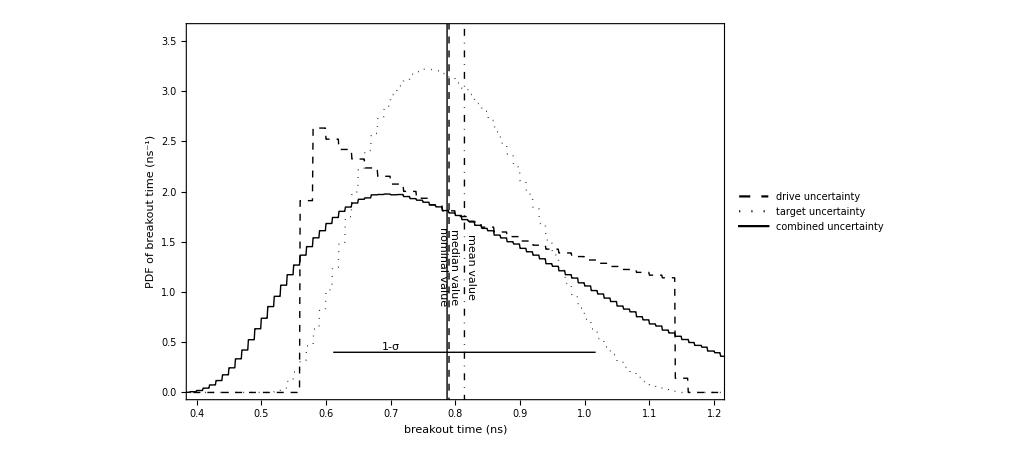

```mathematica
DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,3.6}},Epilog->{Black, line1, Text[Rotate[Style["median value",Black, Medium],-90 Degree],{median + .01,1.25}],Black,DotDashed,line2,Text[Rotate[Style["mean value",Black, Medium],-90 Degree],{mean+.01,1.25}],Black,Dashed, line3, Text[Rotate[Style["nominal value",Black, Medium],-90 Degree],{nominal-.01,1.25}], Black,Dashing[None], line5, Text[Style["1-σ",Black, Medium],{0.7,0.45}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF}
```

```mathematica
Export["UQ_plots/histogramPDF_PN.pdf", plot1];
```

```mathematica
𝒟5N =  HistogramDistribution[allsamples, {0.00001}];
percentilelist = {.20,.40,.50,.60,.80};
```

```mathematica
(*InverseCDF[𝒟5N,percentilelist[[1]]]*)
```

```mathematica
twentieth = InverseCDF[𝒟5N,0.2];
eightieth= InverseCDF[𝒟5N,0.8];
fiftieth = InverseCDF[𝒟5N,0.5];
nominalcdf = CDF[𝒟5N,nominal]
meancdf = CDF[𝒟5N,mean];
```

0.516

```mathematica
For[n =1,n<= 5, n++,Print[InverseCDF[𝒟5N,percentilelist[[n]]]," ", percentilelist[[n]]," percentile"]]
```

0.62408 0.2 percentile

0.74315 0.4 percentile

0.78382 0.5 percentile

0.83488 0.6 percentile

0.99834 0.8 percentile

```mathematica
(*Print[InverseCDF[𝒟5N,0.5]]*)
```

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
```

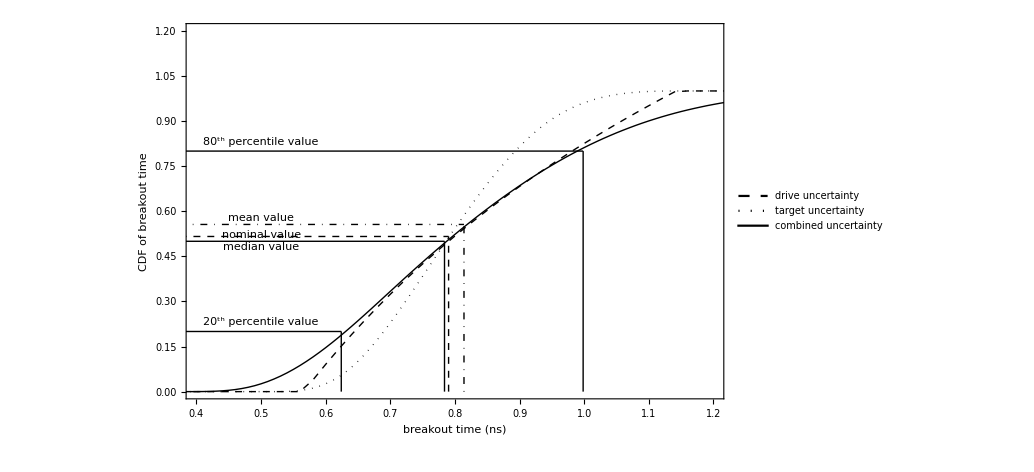

```mathematica
DiscretePlot[{ #[𝒟,x]+shiftδ,#[𝒟2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[𝒟5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.2}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black, Medium],{0.5,0.48}], Text[Style["nominal value",Black, Medium],{0.5,0.52}], Text[Style["mean value",Black, Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black, Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black, Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF}
```

```mathematica
Export["UQ_plots/histogramCDF_PN.pdf", plot2];
```

# Plot: Normal RV breakout PCE expansion

```mathematica
(*SamplingFunctionBreakoutNRV[NBASIS_, NSAMPLES_, drivecoeffs_, densitycoeffs_, bothcoeffs_, allcoeffs_]:= Module[{samples = Table[0,{j,1,NSAMPLES}], densitysamples = Table[0,{j,1,NSAMPLES}],combinedsamples = Table[0,{j,1,NSAMPLES}],meanlist = Table[0,{j,0}],allsamples =Table[0,{j,1,NSAMPLES}], thetasdrive =  Table[0,{j,1,NSAMPLES}], thetasdensity=  Table[0,{j,1,NNN}], θ1list = RandomVariate[NormalDistribution[],NSAMPLES],θ2list = RandomVariate[NormalDistribution[],NSAMPLES],θ3list = RandomVariate[NormalDistribution[],NSAMPLES],θ4list = RandomVariate[NormalDistribution[],NSAMPLES]}, For[i=1, i<=NSAMPLES, i++,
θ1 = θ1list[[i]];
θ2 =θ2list[[i]];
θ3 = θ3list[[i]];
θ4 =  θ4list[[i]];
samples[[i]] =Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2;
 densitysamples[[i]]  =Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS] * xdetector^2;
 (*combinedsamples[[i]]  = Hexpansion[θ1, θ2, θ3, θ4, bothcoeffs, NBASIS] * xdetector^2;*)
allsamples[[i]] = Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS] * xdetector^2;
(*thetasdrive[[i]] = θ1;
thetasdensity[[i]] = θ3;*)
If[Mod[i,NSAMPLES/10]==0,{meanlist =Append[meanlist,{i,Mean[allsamples[[1;;i]]]}],Print[(N[i/NSAMPLES]*100 "%")]}]];
{Re[samples], Re[densitysamples], Re[combinedsamples], Re[allsamples],Re[thetasdrive], thetasdensity,Re[meanlist]}
]*)
```

```mathematica
(*samplefunction[](*:=*)*)
```

```mathematica
SetSharedVariable[samples, densitysamples,allsamples];
```

```mathematica
SamplingFunctionBreakoutNRV[NBASIS_, NSAMPLES_, drivecoeffs_, densitycoeffs_, bothcoeffs_, allcoeffs_]:= Module[{
(*samples = Table[0,{j,1,NSAMPLES}],
 densitysamples = Table[0,{j,1,NSAMPLES}],
combinedsamples = Table[0,{j,1,NSAMPLES}],*)
samples = {},
densitysamples = {},
allsamples={},
meanlist = Table[0,{j,0}],
 thetasdrive =  Table[0,{j,1,NSAMPLES}],
 thetasdensity=  Table[0,{j,1,NSAMPLES}], 
θ1list = RandomVariate[NormalDistribution[],NSAMPLES],
θ2list = RandomVariate[NormalDistribution[],NSAMPLES],
θ3list = RandomVariate[NormalDistribution[],NSAMPLES],
θ4list = RandomVariate[NormalDistribution[],NSAMPLES]},
SetSharedVariable[samples, densitysamples, allsamples];
 ParallelDo[
θ1 = θ1list[[i]];
θ2 =θ2list[[i]];
θ3 = θ3list[[i]];
θ4 =  θ4list[[i]];
(*samples[[i]] =Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2;
 densitysamples[[i]]  =Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS] * xdetector^2;
 (*combinedsamples[[i]]  = Hexpansion[θ1, θ2, θ3, θ4, bothcoeffs, NBASIS] * xdetector^2;*)
allsamples[[i]] = Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS] * xdetector^2;*)
AppendTo[samples, Hexpansion[θ1, θ2, θ3, θ4, drivecoeffs, NBASIS]* xdetector^2];
AppendTo[densitysamples, Hexpansion[θ1, θ2, θ3, θ4, densitycoeffs, NBASIS]* xdetector^2];
AppendTo[allsamples, Hexpansion[θ1, θ2, θ3, θ4, allcoeffs, NBASIS]* xdetector^2];
(*thetasdrive[[i]] = θ1;
thetasdensity[[i]] = θ3;*)
If[Mod[i,NSAMPLES/10]==0,{(*meanlist =Append[meanlist,{i,Mean[allsamples[[1;;i]]]}],*)Print[(N[i/NSAMPLES]*100 "%")]}],{i,NSAMPLES}];
{Re[samples], Re[densitysamples], Re[allsamples],Re[thetasdrive], thetasdensity,Re[meanlist]}
]
```

```mathematica
timelist = {};
```

10. %

20. %

30. %

40. %

50. %

60. %

70. %

80. %

90. %

100. %

```mathematica
(*ListPlot[Hmeanconverge, Joined->True]*)
```

```mathematica
medianH = Median[Hallsamples];
meanH = Mean[Hallsamples]
varH = Variance[Hallsamples];
stdH = Sqrt[varH];
nominalH = Re[Hexpansion[0,0,0,0, allcoeffsH, NN] * xdetector^2];
maxy = 100;
Hline1=Line[{{medianH,-20},{medianH,20}}];
Hline2 = Line[{{meanH,-20},{meanH,maxy}}];
Hline3 = Line[{{nominalH,-20},{nominalH,maxy}}];
(*Hline4 = Line[{{AnalyticBreakout,-20},{AnalyticBreakout,maxy}}];*)
Hline5 = Line[{{meanH- stdH, 0.25}, {meanH+stdH, 0.25}}];
Hline6 = Line[{{meanH - stdH, -20}, {meanH-stdH, 20}}];
(*Plot[{Log[PDF[dist,x]], Log[PDF[dist2,x]], Log[PDF[dist3,x]]},{x,0,xmax},Epilog->{Blue, line1, Text[Style["median",Blue],{median,9}],Red, line2,Text[Style["mean",Red],{mean,9.2}],Orange, line3, Text[Style["nominal",Orange],{nominal,7.6}], Green, line4, Text[Style["analytic expectation",Green],{AnalyticBreakout,7.6}]}, *)(*PlotLegends->{"Drive errors","Density errors", "combined errors"}, AxesLabel->{"time (ns}", "Log bin fraction"}]*)
ℋ= HistogramDistribution[Hsamples, {0.01}];
ℋ2= HistogramDistribution[Hdensitysamples, {0.01}];
(*ℋ3= HistogramDistribution[Hcombinedsamples, {0.01}];*)
(*ℋ4 =  HistogramDistribution[DirectSampleBothParsU, {0.01}];*)
ℋ5 =  HistogramDistribution[Hallsamples, {0.01}];
ℋ5N = HistogramDistribution[Hallsamples, {0.00001}];
For[n =1,n<= 5, n++,Print[InverseCDF[ℋ5N,percentilelist[[n]]]," ", percentilelist[[n]]," percentile"]]
```

0.867156

0.547838 0.2 percentile

0.700995 0.4 percentile

0.780941 0.5 percentile

0.871031 0.6 percentile

1.12816 0.8 percentile

```mathematica
meanH - MakeExpHe[allcoeffsH]
varH - MakeVarHe[13,allcoeffsH]
```

-0.0000426572

-0.000103211-1.20762×10^-10 ⅈ

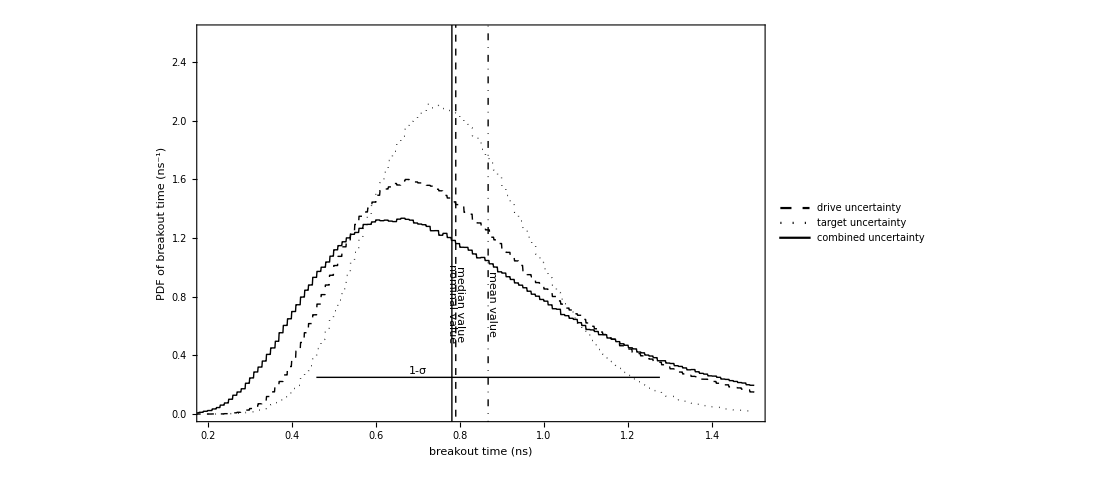

```mathematica
DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.2, 1.5},{0,2.6}},Epilog->{Black, Hline1, Text[Rotate[Style["median value",Black, Medium],-90 Degree],{medianH + .02,.75}],Black,DotDashed,Hline2,Text[Rotate[Style["mean value",Black, Medium],-90 Degree],{meanH+.01,.75}],Black,Dashed, Hline3, Text[Rotate[Style["nominal value",Black, Medium],-90 Degree],{nominalH-.01,.75}], Black,Dashing[None], Hline5, Text[Style["1-σ",Black, Medium],{0.7,0.29}]}, PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["PDF of breakout time (ns^-1)", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{PDF}
```

```mathematica
.
```

```mathematica
ℋ5N =  HistogramDistribution[Hallsamples, {0.00001}];
```

```mathematica
twentieth = InverseCDF[ℋ5N,0.2];
eightieth= InverseCDF[ℋ5N,0.8];
fiftieth = InverseCDF[ℋ5N,0.5];
nominalcdf = CDF[ℋ5N,nominal]
meancdf = CDF[ℋ5N,mean];
```

0.510901

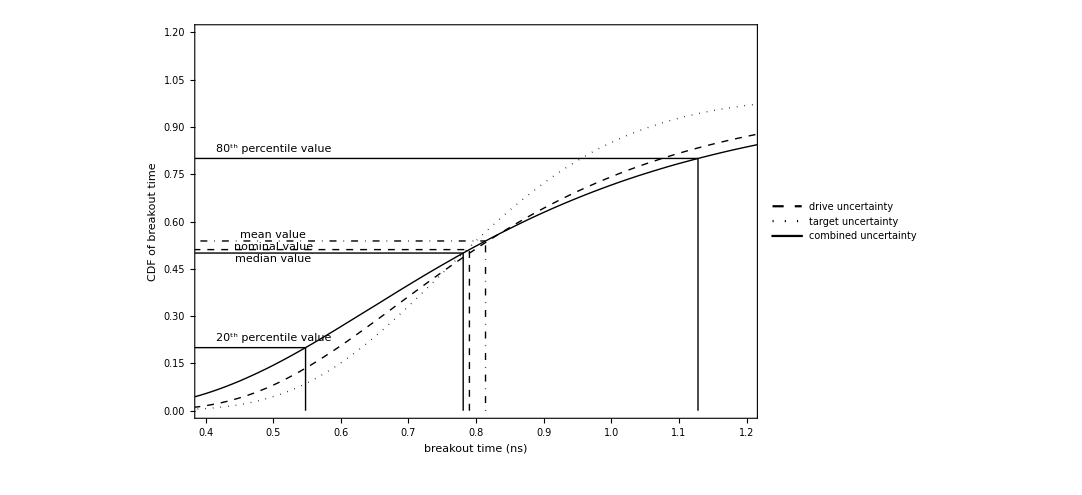

```mathematica
line7 = Line[{{0, 0.5}, {fiftieth, 0.5}}];
line8 = Line[{{fiftieth, 0.0}, {fiftieth, 0.5}}];
line9 = Line[{{0, 0.2}, {twentieth, 0.2}}];
line10 = Line[{{twentieth, 0.0}, {twentieth, 0.2}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line11 = Line[{{0, 0.8}, {eightieth, 0.8}}];
line12 = Line[{{eightieth, 0.0}, {eightieth, 0.8}}];
line13 = Line[{{0, nominalcdf}, {nominal, nominalcdf}}];
line14 = Line[{{nominal, 0.0}, {nominal, nominalcdf}}];
line15 = Line[{{0, meancdf}, {mean, meancdf}}];
line16 = Line[{{mean, 0.0}, {mean, meancdf}}];
DiscretePlot[{ #[ℋ,x]+shiftδ,#[ℋ2,x]+shiftδ,(*#[𝒟3,x],*) (*#[𝒟4,x],*) #[ℋ5,x]+shiftδ},{x,0,1.5,.001},PlotMarkers->{None,None,None,None},(*ScalingFunctions->"Log",*) Filling->None, Joined->{True,True, True, True},PlotRange->{{0.4, 1.2},{0,1.2}}, Epilog->{line7, line8,line9,line10,line11,line12,Dashed, line13,Dashed, line14,DotDashed, line15,DotDashed,line16, Text[Style["median value",Black, Medium],{0.5,0.48}], Text[Style["nominal value",Black, Medium],{0.5,0.52}], Text[Style["mean value",Black, Medium],{0.5,meancdf+0.02}], Text[Style["20^th percentile value",Black, Medium],{0.5,0.23}], Text[Style["80^th percentile value",Black, Medium],{0.5,0.83}]},PlotLegends->{"drive uncertainty","target uncertainty",(* "combined errors",*)(* "Direct sampling combined errors",*) "combined uncertainty"},PlotStyle->styles3, Frame->{True, True, False, False},FrameLabel->{Style["breakout time (ns)", Large],Style["CDF of breakout time", Large]},LabelStyle->Directive[Black, Bold],  BaseStyle->{FontSize->12}]&/@{CDF}
```

# Expensive Tensors

```mathematica
TripleProdHeFunc[i_,j_,k_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i || Abs[j-k]>i || (EvenQ[j+k]&& OddQ[i ]|| OddQ[j+k]&&EvenQ[i]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}]]
QuadrupleProdHeFunc[i_,j_,k_,m_]:= If[(i!= 0 && j!= 0 && k != 0) && j+k<i +m|| Abs[j-k]>i+m || (EvenQ[j+k]&& OddQ[i+m ]|| OddQ[j+k]&&EvenQ[i+m]),0, 1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]HBasis[m,x]Exp[-x^2/2],{x,-∞,∞}]]
```

```mathematica
TripleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn}];
TripleProdHe = ParallelTable[TripleProdHeFunc[i,j,k],{i,0,NHe},{j,0,NHe}, {k,0,NHe}];
```

```mathematica
QuadrupleProdLeg =ParallelTable[ Integrate[Basis[i,x]Basis[j,x]Basis[k,x]Basis[n,x],{x,-1,1}],{i,0,NPn},{j,0,NPn},{k,0,NPn},{n,0,NPn}];
QuadrupleProdHe =ParallelTable[QuadrupleProdHeFunc[i,j,k,n],{i,0,NHe},{j,0,NHe},{k,0,NHe},{n,0,NHe}];
```

# Drive convergence

```mathematica
(*TripleProdHeBlind =ParallelTable[1/Sqrt[2 Pi] Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}],{i,0,NHe},{j,0,NHe},{k,0,NHe}];*)
```

```mathematica
(*MatrixForm[TripleProdHeBlind[[1]]]*)
```

```mathematica
kk=5;
MatrixForm[TripleProdHe[[kk]]-TripleProdHeBlind[[kk]]];
```

```mathematica
(*MatrixForm[TripleProdHeBlind[[3]]]
MatrixForm[TripleProdHe[[3]]]*)
```

```mathematica
(*ii = 1;
testTable=Table[KroneckerDelta[Abs[j-k]-ii]Factorial[Max[j,k]] + KroneckerDelta[(j+k)-ii j](j+k)Factorial[k],   {j,0,NHe},{k,0,NHe}];
factorTable = Table[Factorial[Max[j,k]],{j,0,NHe},{k,0,NHe}];
MatrixForm[testTable]
MatrixForm[TripleProdHe[[2]]-testTable]

MatrixForm[factorTable]*)
MatrixForm[TripleProdHe[[1]]];
MatrixForm[TripleProdHe[[2]]];
MatrixForm[TripleProdHe[[3]]];
MatrixForm[TripleProdHe[[6]]];
```

```mathematica
(* *)
```

```mathematica
(*MatrixForm[TripleProdHe[[3]]-testTable]*)
```

```mathematica
MatrixForm[QuadrupleProdHe[[1]][[1]]];
```

```mathematica
drivecoeffs = MakeCoeffsG[NPn, DrivePars, mh];
drivecoeffsH = MakeCoeffsH[NHe, DrivePars, mh];
```

Table::iterb: Iterator {n,0,NPn} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::iterb: Iterator {ni,0,NHe} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

```mathematica
drivecoeffs[[1]][[1]]drivecoeffs[[2]][[1]]drivecoeffs[[3]][[1]]drivecoeffs[[4]][[1]]*xdetector^2;
drivecoeffsH[[1]][[1]]drivecoeffsH[[2]][[1]]drivecoeffsH[[3]][[1]]drivecoeffsH[[4]][[1]]*xdetector^2;
```

```mathematica
(*Assuming[a1<T0/2&&a1>0 && T0>0,1/2 Integrate[((T0+a1 x)^{-K mh}),{x,-1,1}]]*)
```

```mathematica
FactorialList = Table[Factorial[j],{j,0,NHe}];
LegendreList = Table[1/(2 j+ 1),{j,0, NPn}];
```

```mathematica
ThirdMoment[nn_,AAA_, coeffs_]:= Total[Total[Total[Table[AAA[[i]][[j]][[k]]coeffs[[i]]coeffs[[j]]coeffs[[k]],{i,1,nn}, {j,1,nn},{k,1,nn}]]]]
(*ThirdMoment[nn_,AAA_, coeffs_]:= Integrate[Total[Total[Total[]]],{x,-1,1}]*)
FourthMoment[nn_,AAA_, coeffs_]:=Total[ Total[Total[Total[Table[AAA[[i]][[j]][[k]][[n]]coeffs[[i]]coeffs[[j]]coeffs[[k]]coeffs[[n]],{i,1,nn}, {j,1,nn},{k,1,nn},{n,1,nn}]]]]]
```

```mathematica
MakeSecondMomentHe[nn_, coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]]
```

```mathematica
MakeVarPn[nn_,coeffs_]:=xdetector^4*Total[coeffs[[1]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2LegendreList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2LegendreList[[1;;nn]]] - MakeExpPn[coeffs]^2
MakeVarHe[nn_,coeffs_]:= xdetector^4*Total[coeffs[[1]][[1;;nn]]^2 FactorialList[[1;;nn]]]Total[coeffs[[2]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[3]][[1;;nn]]^2FactorialList[[1;;nn]]]Total[coeffs[[4]][[1;;nn]]^2FactorialList[[1;;nn]]] - (MakeExpHe[coeffs])^2
MakeSkewPn[nn_, coeffs_]:= (1/16 xdetector^6ThirdMoment[nn, TripleProdLeg, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdLeg, coeffs[[4]][[1;;nn]]] - 3 MakeExpPn[coeffs]MakeVarPn[nn, coeffs] -MakeExpPn[coeffs]^3) /(MakeVarPn[nn, coeffs]^(3/2))
MakeSkewHe[nn_, coeffs_]:= ( xdetector^6ThirdMoment[nn, TripleProdHe, coeffs[[1]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[2]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[3]][[1;;nn]]]ThirdMoment[nn, TripleProdHe, coeffs[[4]][[1;;nn]]] - 3 MakeExpHe[coeffs]MakeVarHe[nn, coeffs] -MakeExpHe[coeffs]^3) /(MakeVarHe[nn, coeffs]^(3/2))
MakeKurtPn[nn_, coeffs_]:= (1/16 xdetector^8FourthMoment[nn, QuadrupleProdLeg, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdLeg, coeffs[[4]][[1;;nn]]] - 6(MakeVarPn[nn,coeffs]+MakeExpPn[coeffs]^2)MakeExpPn[coeffs]^2 - 3 MakeExpPn[coeffs]^4)/ MakeVarPn[nn, coeffs]^2
MakeKurtHe[nn_, coeffs_]:= (xdetector^8FourthMoment[nn, QuadrupleProdHe, coeffs[[1]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[2]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[3]][[1;;nn]]]FourthMoment[nn, QuadrupleProdHe, coeffs[[4]][[1;;nn]]] - 6(MakeSecondMomentHe[nn,coeffs])MakeExpHe[coeffs]^2 - 3 MakeExpHe[coeffs]^4)/ MakeVarHe[nn, coeffs]^2
```

```mathematica
(*Exact answers*)

varExact = (DriveBkoutnthMomentPn[2] - DriveBkoutnthMomentPn[1]^2)/.DrivePars;
varExactHe = (DriveBkoutnthMomentHe[2, DrivePars] - DriveBkoutnthMomentHe[1, DrivePars]^2);
skewExact = (DriveBkoutnthMomentPn[3] - 3 DriveBkoutnthMomentPn[1]varExact - DriveBkoutnthMomentPn[1]^3)/varExact^(3/2)/.DrivePars;
skewExactHe = (DriveBkoutnthMomentHeSing[3,DrivePars,δH] - 3 DriveBkoutnthMomentHe[1, DrivePars]varExactHe - DriveBkoutnthMomentHe[1, DrivePars]^3)/varExactHe^(3/2);
kurtExact = (DriveBkoutnthMomentPn[4] - 6 DriveBkoutnthMomentPn[2]DriveBkoutnthMomentPn[1]^2 -3 DriveBkoutnthMomentPn[1]^4)/varExact^(2)/.DrivePars;
δH = 0.5;
kurtExactHe = 1/varExactHe^(2)(DriveBkoutnthMomentHeSing[4,DrivePars,δH] - 6 DriveBkoutnthMomentHe[2, DrivePars]DriveBkoutnthMomentHe[1, DrivePars]^2 -3 DriveBkoutnthMomentHe[1,DrivePars]^4)/.DrivePars;
MakeKurtHe[5, drivecoeffsH];
MakeVarHe[5,drivecoeffsH];
```

```mathematica
converge4thmoment = Table[{j,0},{j,2,9}];
converge3rdmoment = Table[{j,0},{j,2,9}];
```

```mathematica
Print[ DriveBkoutnthMomentPn[1]/.DrivePars," Expected"]
```

0.811267 Expected

```mathematica
Print[varExact," variance Pn"]
Print[skewExact," Skew Pn"]
Print[kurtExact," Kurt Pn"]
Print[DriveBkoutnthMomentHe[1, DrivePars]," Expected He"]
Print[varExactHe," variance He"]
Print[skewExactHe," Skew He"]
Print[kurtExactHe," Kurt He"]
Print[Re[MakeKurtHe[12,drivecoeffsH[[;;]]]]," Kurtosis expansion He"]
```

0.0271596 variance Pn

0.313328 Skew Pn

-4689.77 Kurt Pn

0.858612 Expected He

0.11253 variance He

1.79678-9.04861×10^-12 ⅈ Skew He

-314.628 Kurt He

-317.02 Kurtosis expansion He

```mathematica
(*For[j=2,j<=8, j++,
converge4thmoment[[j]][[2]] = Abs[DriveBkoutnthMomentHe[4,DrivePars ]-xdetector^8FourthMoment[j, QuadrupleProdHe, drivecoeffsH[[1]][[1;;j]]]FourthMoment[j, QuadrupleProdHe, drivecoeffsH[[2]][[1;;j]]]FourthMoment[j, QuadrupleProdHe, drivecoeffsH[[3]][[1;;j]]]FourthMoment[j, QuadrupleProdHe, drivecoeffsH[[4]][[1;;j]]]];
converge3rdmoment[[j]][[2]] = DriveBkoutnthMomentHe[3,DrivePars ]-xdetector^6ThirdMoment[j, TripleProdHe, drivecoeffsH[[1]][[1;;j]]]ThirdMoment[j, TripleProdHe, drivecoeffsH[[2]][[1;;j]]]ThirdMoment[j, TripleProdHe, drivecoeffsH[[3]][[1;;j]]]ThirdMoment[j, TripleProdHe, drivecoeffsH[[4]][[1;;j]]]]*)
```

```mathematica
converge4thmoment;
converge3rdmoment;
```

```mathematica
(*ListLogPlot[{converge4thmoment}, Joined->True, PlotRange->All]*)
(*kurtExactHe*)
```

```mathematica
(*xdetector^4*Total[drivecoeffs[[1]][[1;;nn]]^2LegendreList[[2;;nn]]]Total[drivecoeffs[[2]][[2;;nn]]^2LegendreList[[2;;nn]]]Total[drivecoeffs[[3]][[2;;nn]]^2LegendreList[[2;;nn]]]Total[drivecoeffs[[4]][[2;;nn]]^2LegendreList[[2;;nn]]] - MakeExpPn[drivecoeffs]^2*0*)
```

```mathematica
ERR = Table[0, {k,0,3},{j,NPn-1}];
ERRHe = Table[0, {k,0,3},{j,NHe-1}];
```

```mathematica
(*ThirdMoment[2, TripleProdLeg, drivecoeffs[[1]][[1;;2]]]*)
```

```mathematica
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,drivecoeffs[[;;]]];
skewtest = MakeSkewPn[nn, drivecoeffs[[;;]]];
kurttest = MakeKurtPn[nn,drivecoeffs[[;;]]] ;
ERR[[1]][[nn-1]] = {nn,Abs[(vartest - varExact)]/varExact};
ERR[[2]][[nn-1]]={nn,Abs[(skewtest - skewExact)]/skewExact};
ERR[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExact)]/Abs[kurtExact] };
]
```

```mathematica
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,drivecoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, drivecoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,drivecoeffsH[[;;]]] ;
ERRHe[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHe)]/Abs[varExactHe]};
ERRHe[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHe)]/Abs[skewExactHe]};
ERRHe[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHe)]/Abs[kurtExactHe] };
]
```

```mathematica
ERR[[3]]
```

{{2,0.0288518},{3,0.000268624},{4,2.11499×10^-6},{5,1.52129×10^-8},{6,1.0425×10^-10},{7,5.9188×10^-13},{8,1.05305×10^-13},{9,1.08796×10^-13},{10,1.08796×10^-13},{11,1.08796×10^-13},{12,1.08796×10^-13}}

```mathematica
styles=Flatten@Table[{Directive[color],Directive[Dashed,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
```

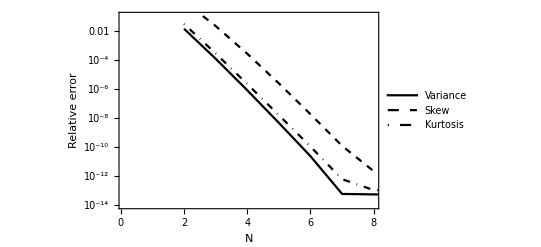

```mathematica
drivePnConvergence = ListLogPlot[{ERR[[1]], ERR[[2]], ERR[[3]]}, Joined->True, PlotRange->{{0.1, NPn-4},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
Export[ "UQ_plots/drivePnConverge.pdf",drivePnConvergence]
```

UQ_plots/drivePnConverge.pdf

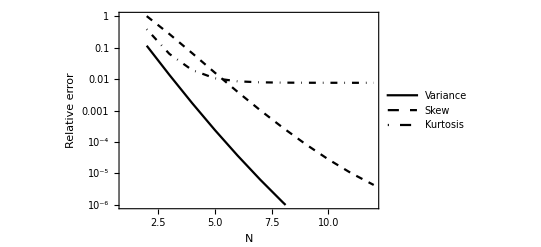

```mathematica
driveHeConvergence = ListLogPlot[{ERRHe[[1]], ERRHe[[2]], ERRHe[[3]]}, Joined->True, PlotRange->{{1, 12},{10^(-6),1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
Export[ "UQ_plots/driveHeConverge.pdf",driveHeConvergence]
```

UQ_plots/driveHeConverge.pdf

```mathematica
drivecoeffsH = MakeCoeffsH[15, DrivePars, mh];
(*styles2=Flatten@Table[{Directive[color, Circle],Directive[Dashed,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];*)
```

```mathematica
drivecoeffs[[1]]
```

{14.04056551972530446814049879369364813178,-4.906831887478327386561214143737424997253,0.7366044425529858247677864474521144157854,-0.08115232037312603828839276350534134505268,0.007549901537855178107365907123888744475035,-0.0006304729982842627586853285981018502595426,0.00004882565243515745472012053577468554859165,-3.576146197298734859611324489098692491109×10^-6,2.509122762555804984713660888954835489975×10^-7,-1.701354838263299395769500136332664382769×10^-8,1.121984394330114658780027094183847939446×10^-9,-7.230119638151464763779934125458218347108×10^-11,4.569162488913032996003315919431235162624×10^-12}

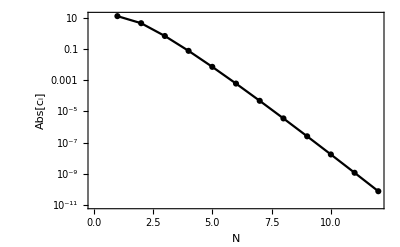

```mathematica
CoeffsDrivePnPlot = ListLogPlot[ Table[{j, Abs[drivecoeffs[[1]][[j]]]},{j,0,NPn}],Joined->True, PlotStyle->styles,Frame->{True, True, False, False},PlotMarkers->Automatic,FrameLabel->{Style["N", Large],Style["Abs[c_i]", Large]},LabelStyle->Directive[Black, Bold]]
(*ListLogPlot[ Re[Table[{j, drivecoeffsH[[2]][[j]]},{j,2,15}]]]*)
```

```mathematica
(*ListLogPlot[{ERRHe[[1]],ERRHe[[2]], ERRHe[[3]]}, Joined->True]*)
```

# Breakout time - all uncertainties

```mathematica
allcoeffsPn = MakeCoeffsG[NPn, AllPars, mh];
allcoeffsH = MakeCoeffsH[NHe, AllPars, mh];
On[Assert]
```

```mathematica
(*Assert[Abs[(N[MakeExpPn[allcoeffsPn]-AllBkoutnthMomentPn[1]/.transfer/.AllPars)]]<=10^{-6}]*)
```

```mathematica
MakeExpPn[allcoeffsPn]-AllBkoutnthMomentPn[1]/.transfer/.AllPars
```

-6.66134×10^-16

```mathematica
(AllBkoutnthMomentPn[2]/.transfer/.AllPars)
nn=10;
```

0.703702

```mathematica
MakeVarPn[1,allcoeffsPn] + MakeExpPn[allcoeffsPn]^2;
```

```mathematica
varExactAll = (AllBkoutnthMomentPn[2] - AllBkoutnthMomentPn[1]^2)/.transfer/.AllPars;
varExactHeAll = (AllBkoutnthMomentHe[2, AllPars] - AllBkoutnthMomentHe[1, AllPars]^2);
skewExactAll = (AllBkoutnthMomentPn[3] - 3 AllBkoutnthMomentPn[1]varExactAll - AllBkoutnthMomentPn[1]^3)/varExactAll^(3/2)/.transfer/.AllPars;

kurtExactAll = (AllBkoutnthMomentPn[4] - 6 AllBkoutnthMomentPn[2]AllBkoutnthMomentPn[1]^2 -3 AllBkoutnthMomentPn[1]^4)/varExactAll^(2)/.transfer/.AllPars;
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.91909486367076573666 and 0.000012308768880001745368 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.86719915648203639452+4.1009068789071826001×10^-22 ⅈ and 0.000018606374569177336728 for the integral and error estimates.

```mathematica
firstmom =AllBkoutnthMomentHeSing[1, AllPars, δH];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.8671985478757172569 and 0.000016786030112411702336 for the integral and error estimates.

```mathematica
MakeExpHe[allcoeffsH]-firstmom
```

-1.00709×10^-7

```mathematica
δH = 0.5;
skewExactHeAll = (AllBkoutnthMomentHeSing[3,AllPars, δH] - 3firstmom varExactHeAll - firstmom^3)/varExactHeAll^(3/2);
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.213393157074393881834189177841290665330292269639074991065721635720826 and 0.00001201030426031681493169148183636330135624397176688796285560527691092722 for the integral and error estimates.

```mathematica
(*AllBkoutnthMomentHe[1, AllPars]*)
```

```mathematica
\
```

```mathematica
kurtExactHeAll = 1/varExactHeAll^(2)(AllBkoutnthMomentHeSing[4,AllPars, δH] - 6AllBkoutnthMomentHe[2, AllPars]firstmom^2 -3 firstmom^4)/.AllPars;
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.055679772336971548289500542395845341932271311182943909415794381801422 and 0.00002713258102970665705522465130982111855071703842052409217134948587033865 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.91909486367076573666 and 0.000012308768880001745368 for the integral and error estimates.

```mathematica
MakeSkewHe[5,allcoeffsH[[;;]]]
```

1.83456+5.11419×10^-10 ⅈ

```mathematica
(*MakeVarPn[5, allcoeffsPn] - varExactAll*)
```

```mathematica
ERRAll = Table[0, {k,0,3},{j,NPn-1}];
ERRHeAll = Table[0, {k,0,3},{j,NHe-1}];
For[nn = 2, nn<=NPn, nn++,
vartest = MakeVarPn[nn,allcoeffsPn[[;;]]];
skewtest = MakeSkewPn[nn, allcoeffsPn[[;;]]];
kurttest = MakeKurtPn[nn,allcoeffsPn[[;;]]] ;
ERRAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactAll)]/varExactAll};
ERRAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactAll)]/skewExactAll};
ERRAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactAll)]/Abs[kurtExactAll] };
]
For[nn = 2, nn<=NHe, nn++,
vartest = MakeVarHe[nn,allcoeffsH[[;;]]];
skewtest = MakeSkewHe[nn, allcoeffsH[[;;]]];
kurttest = MakeKurtHe[nn,allcoeffsH[[;;]]] ;
ERRHeAll[[1]][[nn-1]] = {nn,Abs[(vartest - varExactHeAll)]/varExactHeAll};
ERRHeAll[[2]][[nn-1]]={nn,Abs[(skewtest - skewExactHeAll)]/skewExactHeAll};
ERRHeAll[[3]][[nn-1]] = {nn, Abs[(kurttest - kurtExactHeAll)]/Abs[kurtExactHeAll] };
]
```

```mathematica
ERRHeAll[[1]]
```

{{2,0.0846659},{3,0.00987105},{4,0.00125411},{5,0.00017196},{6,0.0000232171},{7,6.99678×10^-7},{8,3.06136×10^-6},{9,3.75448×10^-6},{10,3.89536×10^-6},{11,3.92693×10^-6},{12,3.93476×10^-6}}

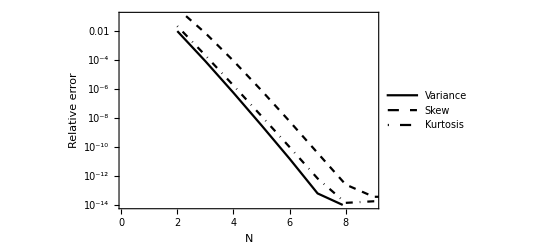

```mathematica
AllPnConvergence = ListLogPlot[{ERRAll[[1]], ERRAll[[2]], ERRAll[[3]]}, Joined->True, PlotRange->{{0.1, NPn-3},{10^(-14),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
Export[ "UQ_plots/AllPnConverge_10.pdf",AllPnConvergence]
```

UQ_plots/AllPnConverge_10.pdf

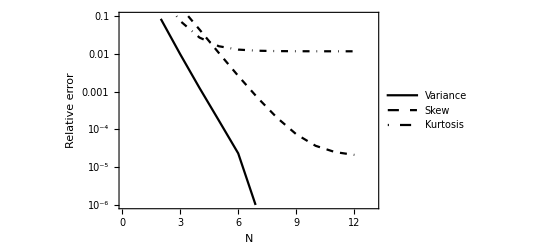

```mathematica
AllHeConvergence = ListLogPlot[{Re[ERRHeAll[[1]][[1;;6]]], ERRHeAll[[2]], ERRHeAll[[3]]}, Joined->True, PlotRange->{{0.1, NHe+1},{10^(-6),0.1}}, PlotStyle->styles, Frame->{True, True, False, False},FrameLabel->{Style["N", Large],Style["Relative error", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"Variance", "Skew", "Kurtosis"}]
```

```mathematica
Export[ "UQ_plots/AllHeConverge.pdf",AllHeConvergence]
```

UQ_plots/AllHeConverge.pdf

```mathematica
styles2=Flatten@Table[{Directive[color],Directive[color],Directive[color],Directive[color]},{color,{Black,Gray}} ];
```

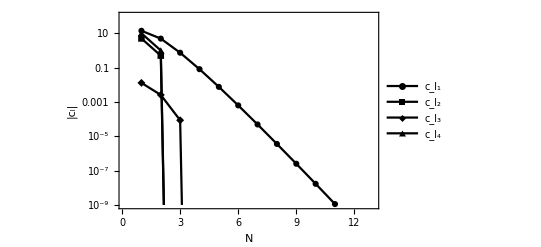

```mathematica
CoeffsAllPnPlot = ListLogPlot[{ Table[{j, Abs[allcoeffsPn[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsPn[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsPn[[3]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsPn[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
```

```mathematica
Export["UQ_plots/CoeffsAllUncertainPn_10.pdf",CoeffsAllPnPlot]
```

UQ_plots/CoeffsAllUncertainPn_10.pdf

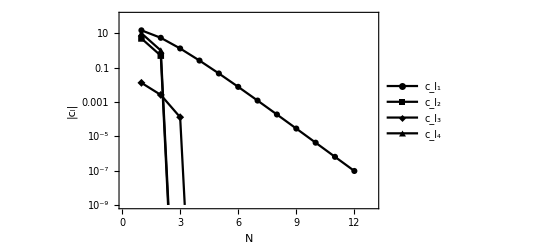

```mathematica
CoeffsAllHePlot = ListLogPlot[{ Table[{j, Abs[allcoeffsH[[1]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[2]][[j]]]},{j,0,NPn}], Table[{j, Abs[allcoeffsH[[3]][[j]]]},{j,0,NHe+1}], Table[{j, Abs[allcoeffsH[[4]][[j]]]},{j,0,NPn}]},Joined->True, PlotStyle->styles2,Frame->{True, True, False, False},PlotMarkers->Automatic, PlotRange->{{0.1, NPn+1},{10^(-9),100}}, FrameLabel->{Style["N", Large],Style["|c_l|", Large]},LabelStyle->Directive[Black, Bold], PlotLegends->{"c_l_1","c_l_2", "c_l_3", "c_l_4"}]
```

```mathematica
(*Abs[allcoeffsPn[[4]][[4]]]*)
```

```mathematica
Export["UQ_plots/CoeffsAllUncertainHe_10.pdf",CoeffsAllHePlot]
```

UQ_plots/CoeffsAllUncertainHe_10.pdf

```mathematica
Print[MakeExpPn[allcoeffsPn]," Expected Pn"]
```

0.813972 Expected Pn

```mathematica
Print[varExactAll," variance Pn"]
Print[skewExactAll," Skew Pn"]
Print[kurtExactAll," Kurt Pn"]
Print[MakeExpHe[allcoeffsH] ," Expected He"]
Print[varExactHeAll," variance He"]
Print[skewExactHeAll," Skew He"]
Print[kurtExactHeAll," Kurt He"]
Print[MakeSkewHe[NHe, allcoeffsH[[;;]]], " " , NHe   " term expansion skew"]
Print[MakeKurtHe[NHe,allcoeffsH[[;;]]], " ",  NHe   " term expansion kurtosis"]
```

0.0411526 variance Pn

0.551611 Skew Pn

-2061.97 Kurt Pn

0.867198 Expected He

0.167060486667610291 variance He

1.8541612948970255 Skew He

-135.730207719584281 Kurt He

1.85412+1.64383×10^-7 ⅈ 12  term expansion skew

-137.319+0.000015122 ⅈ 12  term expansion kurtosis

# Sensitivity of Breakout to polynomial Order

```mathematica
g1g =  g1coeffs[11,AllPars,m,1];
g2g = g2coeffs[11,AllPars,1];
g3g = g3coeffs[11,AllPars,1];
g4g = g4coeffs[11,AllPars,1];
```

```mathematica
totalexpansionNN[0,0,0,0,10, BothPars, g1g,g2g ,g3g, g4g]-totalexpansion[0,0,0,0]*xdetector^2
```

-0.09 totalexpansion[0,0,0,0]+totalexpansionNN[0,0,0,0,10,{T0→0.4,ξ→1.1111,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0,a3→0.01134,a4→0,ω→1.04763},{18.72075402630040501880567770905844902861,-6.542442516637769520690514154746856954147,0.9821392567373143837762950649113739089562,-0.1082030938308347122922280228363054766937,0.01006653538380690363838814174645689394585,-0.0008406306643790169694286849284853962033726,0.00006510086991354326969580703547810832761697,-4.768194929731646240390112046026728204925×10^-6,3.345497016741073145198251946502299283891×10^-7,-2.268473117684399080611259533822393944565×10^-8,1.49597919244015280336046737530691742875×10^-9,-9.640159517535285868319947780828628833885×10^-11},{4.992416209637762669615312915993854403496,0.4992416209637762780637615378509508445859,-1.284558962640835627659570353859640017004×10^-56,-9.960544134508484534965776156515407303622×10^-57,-7.891360869532506282801432864598119654179×10^-56,-1.312071679583102124097817458752903568182×10^-56,-1.1714939612279285072255638107034744905×10^-55,-1.134573606071766280199393151678082956069×10^-56,1.547953018542451389628552304896162906584×10^-55,-1.953923692533265607750285185425852727257×10^-55,-1.218956972195079926256007254383034406849×10^-54,5.736212135701150033517543606832834820765×10^-55},{0.01290242520000000018976800131298432567104,0.002571912000000000272320166416761823684377,0.0000857304000000000169460445675895252140889,5.499963460498007199916846386914608541465×10^-59,-3.46449954256505987164732951971546839885×10^-58,-3.919830393077680373410592542337433815618×10^-58,-6.013377621817162759913166766351513390256×10^-58,-2.020778851648821867960823225302675927729×10^-58,1.892616328576533040961046781356722909002×10^-57,-5.330061330895946891895353466356987709438×10^-57,-9.051875763759858982049077080822166265621×10^-57,1.162182836590683625332514824342910032471×10^-56},{10.,1.,-2.557654635940127131096412708943669200256×10^-56,-1.998486757937983556747738541563484372554×10^-56,-1.581682903121572493943086285231115097237×10^-55,-2.60613560436344089967803744843567509884×10^-56,-2.343575825566473917276852734795830796916×10^-55,-2.3673180405812421297121325371821085164×10^-56,3.100326829025344606084455136664268141405×10^-55,-3.843203010869127336930036494350571671057×10^-55,-2.44390820287790801118700964503087648161×10^-54,1.152399611130305222345088506299789882327×10^-54}]

```mathematica
g1g =  g1coeffs[11,DrivePars,m,1];
g2g = g2coeffs[11,DrivePars,1];
g3g = g3coeffs[11,DrivePars,1];
g4g = g4coeffs[11,DrivePars,1];
```

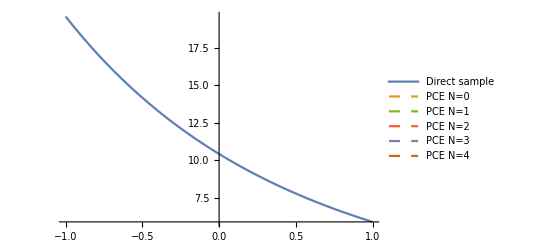

```mathematica
plot4 = Plot[{BreakoutTimeU[x, 0, 0, 0, DrivePars, xdetector]/.n->m,totalexpansionNN[x,0,0,0,0, DrivePars, g1g,g2g ,g3g, g4g], totalexpansionNN[x,0,0,0,1, DrivePars, g1g,g2g ,g3g, g4g] ,totalexpansionNN[x,0,0,0,2, DrivePars, g1g,g2g ,g3g, g4g], totalexpansionNN[x,0,0,0,3, DrivePars, g1g,g2g ,g3g, g4g], totalexpansionNN[x,0,0,0,4, DrivePars, g1g,g2g ,g3g, g4g]},{x,-1,1},PlotLegends->{ "Direct sample", "PCE N=0", "PCE N=1", "PCE N=2", "PCE N=3", "PCE N=4", "PCE N=5"}, PlotStyle->{Thick, Dashed, Dashed, Dashed, Dashed,Dashed, Dashed},BaseStyle->{FontSize->12}]
```

```mathematica
g1g =  g1coeffs[11,DensityPars,m,1];
g2g = g2coeffs[11,DensityPars,1];
g3g = g3coeffs[11,DensityPars,1];
g4g = g4coeffs[11,DensityPars,1];
```

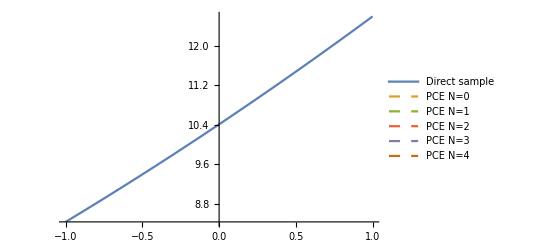

```mathematica
plot5 = Plot[{BreakoutTimeU[0, 0, x, 0, DensityPars, xdetector]/.n->m,totalexpansionNN[0,0,x,0,0, DensityPars, g1g,g2g ,g3g, g4g], totalexpansionNN[0,0,x,0,1, DensityPars, g1g,g2g ,g3g, g4g] ,totalexpansionNN[0,0,x,0,2, DensityPars, g1g,g2g ,g3g, g4g], totalexpansionNN[0,0,x,0,3, DensityPars, g1g,g2g ,g3g, g4g], totalexpansionNN[0,0,x,0,4, DensityPars, g1g,g2g ,g3g, g4g]},{x,-1,1},PlotLegends->{ "Direct sample", "PCE N=0", "PCE N=1", "PCE N=2", "PCE N=3", "PCE N=4", "PCE N=5"}, PlotStyle->{Thick, Dashed, Dashed, Dashed, Dashed,Dashed, Dashed},BaseStyle->{FontSize->12}]
```

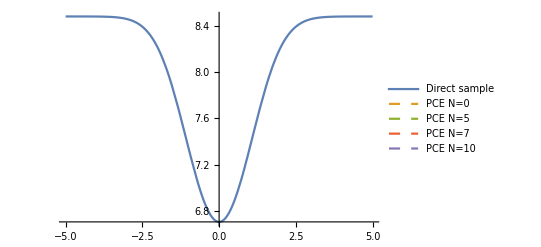

```mathematica
plot5 = Plot[{BreakoutTimeG[x, 0, 0, 0, DriveParsH, xdetector]/.n->mh,totalexpansionNNHermite[x,0,0,0, 0, DriveParsH, Hcoeffs1, Hcoeffs2, Hcoeffs3, Hcoeffs4], totalexpansionNNHermite[x,0,0,0, 5, DriveParsH, Hcoeffs1, Hcoeffs2, Hcoeffs3, Hcoeffs4], totalexpansionNNHermite[x,0,0,0, 7, DriveParsH, Hcoeffs1, Hcoeffs2, Hcoeffs3, Hcoeffs4],totalexpansionNNHermite[x,0,0,0, 10, DriveParsH, Hcoeffs1, Hcoeffs2, Hcoeffs3, Hcoeffs4]},{x,-5,5},PlotLegends->{ "Direct sample", "PCE N=0", "PCE N=5", "PCE N=7", "PCE N=10", "PCE N=5"}, PlotStyle->{Thick, Dashed, Dashed, Dashed, Dashed,Dashed, Dashed},BaseStyle->{FontSize->12}]
```

# PCE of the temperature profile

```mathematica
intvarfourthorder[l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_] := Integrate[Basis[l1,x1]Basis[l2,x2]Basis[l3,x3]Basis[l4,x4]Basis[l5,x1]Basis[l6,x2]Basis[l7,x3]Basis[l8,x4],{x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1}]
```

```mathematica
intvarfourthorder[2,2,2,2,2,2,2,2]
```

16/625

16/625

```mathematica
nm = 7/2;
aJonas = 7.5657*10^(−15);
cJonas = 299792458.0*100.0;
aJonas = 4 * 5.6704*10^(-5)/cJonas;
tjonas =1*3.0888*10^(-8);
ξmaxt = ξmaxn72;
tol = 1*10^(-4);
(*tval = 0.6;*)
(*tval = tjonas;*)
tval = 0.8;
Nevalpoints = 50;
(*DriveParsnew = {T0->T0val,κ0->κ0val, ρ0-> ρ0val,cv->cv0val,a1->0.3 * T0val, a2->0, a3->0, a4->0,ω->omegaval, n->mh};*)
DriveParsnew = {T0->80*10^(-3),κ0->107991, ρ0-> 1,cv->8310*10^(-16)*(11604)*10^3,a1->0.1 * T0val, a2->0, a3->0.0, a4->0,ω->omegavaln0, n->0, ξ->ξmaxn72};
BothParsnew = {T0->80*10^(-3),κ0->107991, ρ0-> 1,cv->8310*10^(-16)*(11604)*10^3,a1->0.1 * T0val, a2->0, a3->0.1*1, a4->0,ω->omegavaln0, n->0, ξ->ξmaxn0};

AAfunc[ pars_,x1_, x2_, x3_, x4_]:= Sqrt[((κ0 + a2 x2)   (cv + a4 x4)( ρ0 + a3 x3)^2)/(T0 + a1 x1)^(n)]  / ω/.pars;
```

```mathematica
ICS[ξmax_, ξ_] := {T[ξmax]==1/5((nm+3)*ξmax*(-ξ+ξmax)/(nm+4))^(1/(nm+3)), u[ξmax]==-(((nm+3)/(nm+4))*ξmax)^(1/(nm+3))*1/(nm+3)*(ξmax-ξ)^((-2-nm)/(nm+3))1/5}
eqsMarshak = {D[T[ξ],ξ]==u[ξ], D[u[ξ],ξ] ==- u[ξ]*((T[ξ]^(-nm)*ξ)/(nm+4)+(nm+3)*T[ξ]^2*u[ξ])/(T[ξ]^3)} ;
bcs = {T[0]==1};
```

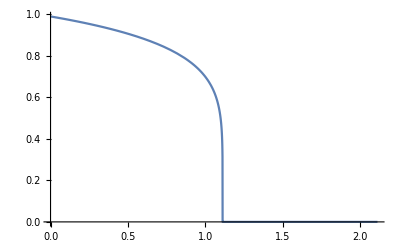

```mathematica
sol=NDSolve[{eqsMarshak,ICS[ξmaxt,ξmaxt-tol]},{T[ξ],u[ξ]},{ξ,0,ξmaxt-tol},Method->{"Shooting","StartingInitialConditions"->{T[ξmaxt]==ICS[ξmaxt,ξmaxt-tol][[1]],u[ξmaxt]==ICS[ξmaxt,ξmaxt-tol][[2]]}}];
Clear[Tsol2]
Tsol2[ξξ_?NumericQ] :=Piecewise[{{((T[ξ]/.sol)/.ξ->ξξ )[[1]],0<=ξξ<=ξmaxt},{0,True}}]
Plot[{ Tsol2[x]},{x,0,ξmaxt + 1}]
(*Plot[{ Tsol2[x]^4},{x,0,ξmaxt + 1}]*)
(*T0expand = 0.05;
Series[T^4, {T,T0,4}]
Plot[{T0expand^4+4 T0expand^3 (Tsol2[x]-T0expand),Tsol2[x]^4},{x,ξmaxt-0.001,ξmaxt }]*)
```

```mathematica
T0funcU[x_, pars_]:=( T0 + a1 x)/.pars
ξfunc[AA_, x_, t_] := AA x/Sqrt[t] 
xpos = ξmaxn0 Sqrt[tval]/AAfunc[DrivePars, 0, 0, 0, 0];
```

ReplaceAll::reps: {DriveParsnew} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
fakepars = {T0->Subscript[T, 0] ,ρ0 -> Subscript[ρ, 0],cv->Subscript[C, v] ,κ0 -> Subscript[κ, 0], a1-> Subscript[a, 1], a2->0, a3->0, a4->0};
```

```mathematica
IntegrandFunc2[x_,t_,pars_, x1_, x2_, x3_, x4_] := Tsol2[ξfunc[AAfunc[pars, x1, x2, x3, x4],x, t]] * T0funcU[x1, pars]
IntegrandFunc2[0.2,tval,DrivePars, 1, 0, 0, 0]
```

0.385817

```mathematica
xlist = N@Subdivide[0,xpos +0.05,Nevalpoints];
xlist2 = N@Subdivide[0,xpos + 0.05,25];
```

```mathematica
analyticProfile[x_,t_, pars_] := 1/2 NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0, 0, 0],{xx1, -1,1}, WorkingPrecision->14]
analyticProfileDensity[x_,t_, pars_] := 1/8 NIntegrate[IntegrandFunc2[x,t,pars, 0, xx2, xx3, xx4],{xx2, -1,1},{xx3, -1,1},{xx4,-1,1}, WorkingPrecision->14]
tempNthMomentPn[x_,t_, pars_, k_] := 1/16 NIntegrate[IntegrandFunc2[x,t,pars, xx1, xx2, xx3, xx4]^k,{xx1,-1,1},{xx2, -1,1},{xx3, -1,1},{xx4,-1,1}, WorkingPrecision->14]
```

```mathematica
data=  ParallelTable[{xlist[[ix]],Quiet[analyticProfile[xlist[[ix]],tval, DrivePars]]},{ix, 1, Nevalpoints}];
```

```mathematica
expectedAllPn = ParallelTable[{xlist[[ix]],Quiet[tempNthMomentPn[xlist[[ix]],tval, AllPars,1]]},{ix, 1, Nevalpoints}];
```

```mathematica
varianceAllPn = ParallelTable[{xlist[[ix]],Quiet[tempNthMomentPn[xlist[[ix]],tval, AllPars,2]-expectedAllPn[[ix,2]]^2]},{ix, 1, Nevalpoints}];
```

```mathematica
stdAllPnp = Table[{xlist[[ix]],expectedAllPn[[ix,2]]+Sqrt[varianceAllPn[[ix,2]]] },{ix, 1, Nevalpoints}];
stdAllPnm = Table[{xlist[[ix]], expectedAllPn[[ix,2]]-Sqrt[varianceAllPn[[ix,2]]]},{ix, 1, Nevalpoints}];
```

```mathematica
dataDriveDensity=  ParallelTable[{xlist[[ix]],Quiet[analyticProfileDensity[xlist[[ix]],tval, DensityPars]]},{ix, 1, Nevalpoints}];
```

```mathematica
Sqrt[varianceAllPn[[1,2]]]
```

0.022868269598

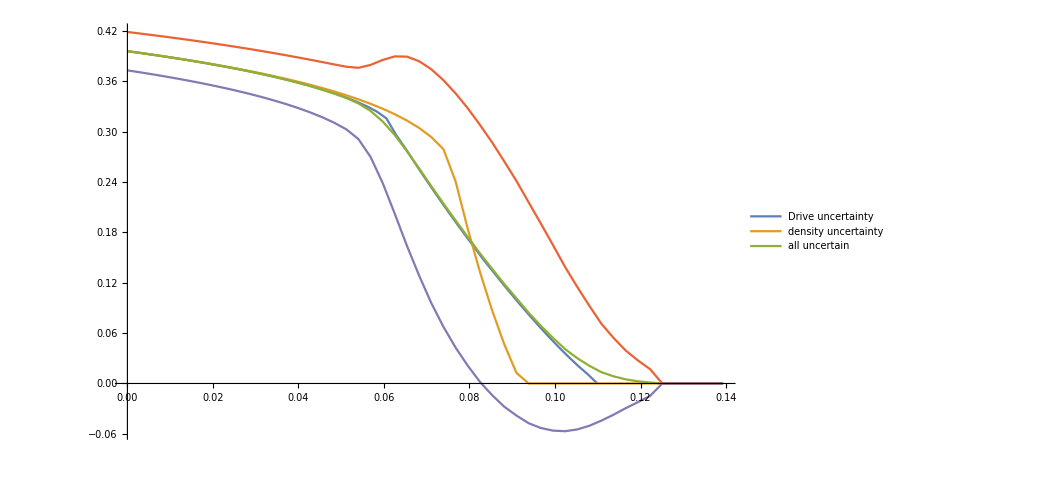

```mathematica
ListPlot[{data, dataDriveDensity, expectedAllPn, stdAllPnp, stdAllPnm}, Joined->True, PlotLegends->{"Drive uncertainty", "density uncertainty", "all uncertain"}]
```

# PCE OF Wave -- Drive uncertainty

```mathematica
MBASIS = 3;
SAMPLES = 50000;
```

```mathematica
MakeICDF[samples_, quart_, TMAX_]:= Module[{icdf=InverseCDF[HistogramDistribution[samples],x]} ,icdf/.x->quart]
```

```mathematica
𝒫[θ1_, M_, l1_]:= Basis[l1,θ1]
𝒫4[θ1_,θ2_,θ3_,θ4_, l1_,l2_,l3_,l4_]:= Basis[l1,θ1] Basis[l2,θ2] Basis[l3,θ3] Basis[l4,θ4]
```

```mathematica
(*𝒞[x_, t_, pars_, MM_] := Table[NIntegrate[IntegrandFunc2[x,t,pars, θ1, θ2,θ3, θ4]𝒫[θ1, θ2, θ3, θ4, MM, l1, l2, l3, l4],{θ1,-1,1},{θ2,-1,1}, {θ3,-1,1}, {θ4,-1,1}, AccuracyGoal->10],{l1,0, MM}, {l2,0,MM}, {l3,0,MM},{l4,0,MM}]*)
𝒞[x_, t_, pars_, MM_] := ParallelTable[Quiet[NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0,0, 0]Basis[l1-1, xx1],{xx1,-1,1},   AccuracyGoal->12, WorkingPrecision->12]],{l1,1, MM+1}]
```

```mathematica
(*Expansion[θ1_,θ2_,θ3_,θ4_,  pars_, MM_, coeffs_] :=
									Sum[𝒫[θ1, MM, l1] coeffs[[l1+1]],{l1,0,MM}]*)
Expansion[θ1_,θ2_,θ3_,θ4_,  pars_, MM_, coeffs_] :=
									Total[Table[Basis[l1-1,θ1] coeffs[[l1]],{l1,1,MM+1} ]]
```

```mathematica
CC = Table[0, {j,1,Nevalpoints}];
For[ix = 1, ix <= Nevalpoints, ix ++,
CC[[ix]] = 𝒞[xlist[[ix]], tval, DriveParsnew, MBASIS]]
```

```mathematica
DriveSamples = Table[0, {j, 1, Nevalpoints},{k,0,SAMPLES}];
```

```mathematica
dataDrive = Table[0, {j,1, Nevalpoints}];
sobolsequence = sobol[SAMPLES, 2];
```

```mathematica
For[iterator = 1, iterator <= Nevalpoints, iterator ++,
xtest = xlist[[iterator]];
CCC = CC[[iterator]];
sampleslist = Table[0, {jj, 1, SAMPLES}];
For[ns =1, ns<= SAMPLES, ns ++,
(*x1 = RandomReal[{-1,1}];
x3 = RandomReal[{-1,1}];*)
x1 = sobolsequence[[ns,1]]*2 -1;
x3 = sobolsequence[[ns,2]]*2 - 1;
DriveSamples[[iterator, ns]] = Expansion[ x1,0,0,0,  DriveParsnew, MBASIS,CCC];
];
dataDrive[[iterator]] = {xtest, Mean[DriveSamples[[iterator]]]}]

sampleslist;
meanlist;
data;
exact = Table[{xlist[[j]],CC[[j,1]] Basis[0,0]}, {j, 1, Nevalpoints}];
```

Make PDF’s of the samples at  each x point:

```mathematica
dataDrive20 = Table[0, {j, Nevalpoints}];
dataDrive80 = Table[0, {j, Nevalpoints}];
```

```mathematica
tdrive = T0/.DriveParsnew;
```

```mathematica
For[ix=1, ix<=Nevalpoints, ix++,
dataDrive20[[ix]] = {xlist[[ix]],MakeICDF[DriveSamples[[ix]], 0.20, tdrive]};
dataDrive80[[ix]] = {xlist[[ix]],MakeICDF[DriveSamples[[ix]], 0.80, tdrive]};
If[dataDrive20[[ix]][[2]] >dataDrive20[[1]] [[2]], dataDrive20[[ix]] [[2]]= 0];
If[dataDrive80[[ix]][[2]] >dataDrive80[[1]][[2]], dataDrive80[[ix]][[2]] = 0];
]
```

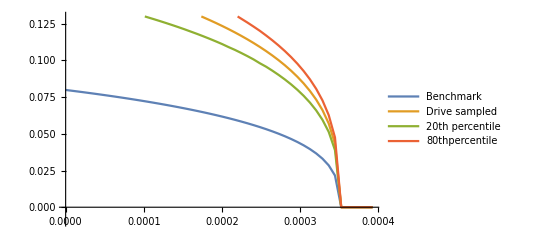

```mathematica
ListPlot[{ data ,(*exact,*) dataDrive, dataDrive20, dataDrive80}, {Joined->True, Joined->False}, PlotRange->{{0, xlist[[Nevalpoints]]},{-0.01, 0.13}}, PlotLegends->{"Benchmark",(*"C0",*) "Drive sampled", "20th percentile", "80thpercentile"}]
```

```mathematica
Print[RMSE[data[[1;;,2]], dataDrive[[1;;,2]]]," Sampled RMSE"];
Print[RMSE[data[[1;;,2]], exact[[1;;,2]]]," Exact RMSE"];
```

0.0593913 Sampled RMSE

0.059394807244 Exact RMSE

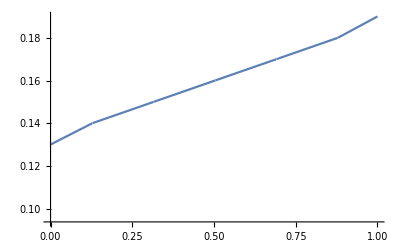

```mathematica
DD = HistogramDistribution[DriveSamples[[1]],{0.01}];
Plot[InverseCDF[DD,x],{x,0,1}]
```

```mathematica
InverseCDF[DD,x]/.x->0.2
```

0.143837

# PCE of temperature profile -- Both uncertainties

```mathematica
𝒫2[θ1_,θ3_, M_, l1_, l3_]:= Basis[l1,θ1]Basis[l3,θ3 ]
𝒞2[x_, t_, pars_, MM_] := ParallelTable[Quiet[NIntegrate[IntegrandFunc2[x,t,pars, xx1, 0,xx3, 0]𝒫2[xx1,xx3,MM, l1-1, l3-1],{xx1,-1,1},{xx3,-1,1},   AccuracyGoal->12, WorkingPrecision->12]],{l1,1, MM+1},{l3,1, MM+1} ]
𝒞4[x_, t_, pars_, MM_] := ParallelTable[NIntegrate[(IntegrandFunc2[x,t,pars, xx1, xx2,xx3, xx3]/.n->mh )𝒫4[xx1,xx2,xx3,xx4, l1-1,l2-1, l3-1,l4-1],{xx1,-1,1},{xx2,-1,1},{xx3,-1,1},{xx4,-1,1},   AccuracyGoal->8],{l1,1, MM+1},{l2,1, MM+1},{l3,1, MM+1} ,{l4,1, MM+1}]
Expansion2[θ1_,θ2_,θ3_,θ4_,  pars_, MM_, coeffs_] :=
									Sum[𝒫2[θ1,θ3, MM, l1-1, l3-1] coeffs[[l1]][[l3]],{l1,1,MM+1},{l3,1,MM+1} ]
```

```mathematica
analyticA =Limit[ExpectedValueoneoverA ,{Subscript[a, 2]->0,  Subscript[a, 4]->0}]/.{Subscript[a, 1]->a1, Subscript[a, 3]->a3, ρ̄->ρ0, OverBar[Subscript[c, v]]->cv, κ̄->κ0, T̄->T0, n->0, ξ->ξmaxn0, ω->omegavaln0}/.BothParsnew
AnalyticFront = analyticA * Sqrt[tval]
```

2.00518

0.000352409

```mathematica
𝒞2[0, tval, BothParsnew, 2][[1,3]]
```

-1.67787763733×10^-18

```mathematica
CC2 = Table[0, {j,1,Nevalpoints}];
For[ix = 1, ix <= Nevalpoints, ix ++,
CC2[[ix]] = 𝒞2[xlist[[ix]], tval, BothParsnew, MBASIS];
Print[CC2[[ix]]];
Print[xlist[[ix]]];
]
```

```mathematica
AllPars
```

{T0→0.4,ξ→1.1111,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097}

```mathematica
𝒞4[xlist[[10]], tval, AllPars, 2]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.000286308 and 3.59519×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000715769 and 8.98797×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0692074,0.8,{T0→0.4,ξ→1.1111,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.64522×10^-8 and 0.000035811 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000165226 and 1.8002×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.13066×10^-6 and 4.5005×10^-8 for the integral and error estimates.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0692074,0.8,{T0→0.4,ξ→1.1111,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.86479×10^-7 and 3.81214×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.6712×10^-9 and 0.0000180089 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.32706×10^-6 and 1.34647×10^-7 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.31764×10^-7 and 3.36617×10^-8 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::oidiv: The odd integrand (IntegrandFunc2[0.0692074,0.8,{T0→0.4,ξ→1.1111,κ0→4.99242,ρ0→0.1134,cv→10,a1→0.04,a2→0.499242,a3→0.01134,a4→1.,ω→1.2097},xx1,xx2,xx3,xx3]/.n→mh) 𝒫4[xx1,xx2,xx3,xx4,l1-1,l2-1,l3-1,l4-1] is being considered as zero over the specified region, but may actually be divergent.

$Aborted

```mathematica
CC4 = Table[0, {j,1,Nevalpoints}];
Do[
CC4[[ix]] = 𝒞4[xlist[[ix]], tval, AllPars, 2];
Print[CC4[[ix]]];
Print[xlist[[ix]]];
,{ix,Nevalpoints}]
```

ParallelTable::subpar: Parallel computations cannot be nested; proceeding with sequential evaluation.

$Aborted

```mathematica
CC2[[1]][[1]][[1]]Basis[0,0]^2
```

0.0799103343993

```mathematica
Expansion2[0,0,0,0,  BothParsnew, MBASIS, CC2[[1]]]
```

0.0799103343993

```mathematica
BothSamples = Table[0, {j, 1, Nevalpoints},{k,0,SAMPLES}];
dataBoth = Table[0, {j,1, Nevalpoints}];
```

```mathematica
For[iterator = 1, iterator <= Nevalpoints, iterator ++,
xtest = xlist[[iterator]];
CCC = CC2[[iterator]];
sampleslist = Table[0, {jj, 1, SAMPLES}];
For[ns =1, ns<= SAMPLES, ns ++,
(*x1 = RandomReal[{-1,1}];
x3 = RandomReal[{-1,1}];*)
x1 = sobolsequence[[ns,1]]*2 -1;
x3 = sobolsequence[[ns,2]]*2 - 1;
BothSamples[[iterator, ns]] = Expansion2[ x1,0,x3,0,  BothParsnew, MBASIS,CCC];
];
dataBoth[[iterator]] = {xtest, Mean[BothSamples[[iterator]]]}]
sampleslist;
meanlist;
data;
exactBoth = Table[{xlist[[j]],CC2[[j]][[1]][[1]] Basis[0,0] Basis[0,0]}, {j, 1, Nevalpoints}];
```

```mathematica
dataBoth20 = Table[0, {j, Nevalpoints}];
dataBoth80 = Table[0, {j, Nevalpoints}];
For[ix=1, ix<=Nevalpoints, ix++,
dataBoth20[[ix]] = {xlist[[ix]],MakeICDF[BothSamples[[ix]], 0.20, tdrive]};
dataBoth80[[ix]] = {xlist[[ix]],MakeICDF[BothSamples[[ix]], 0.80, tdrive]};
If[dataBoth20[[ix]][[2]] >dataBoth20[[1]] [[2]], dataBoth20[[ix]] [[2]]= 0];
If[dataBoth20[[ix]][[2]] <0, dataBoth20[[ix]] [[2]]= 0]
If[dataBoth80[[ix]][[2]] >dataBoth80[[1]][[2]], dataBoth80[[ix]][[2]] = 0];
]
maxlist = { AnalyticFront,0}
line1=Line[{{AnalyticFront,-20},{AnalyticFront,10}}];
```

{0.000352409,0}

```mathematica
0funcU[x_, pars_]:=( T0 + a1 x)/.pars
ξfunc[AA_, x_, t_] := AA x/Sqrt[t]
```

```mathematica
tval
```

3.0888×10^-8

```mathematica
T0funcU[0, BothParsnew]
ξfunc[AAfunc[BothParsnew,0,0,0,0], xlist[j], tval]
```

0.616057

2/25

```mathematica
Tnominal = Table[{xlist[[j]],Tsol2[ξfunc[AAfunc[BothParsnew,0,0,0,0], xlist[[j]], tval]]T0funcU[0, BothParsnew]},{j,1, Nevalpoints}];
```

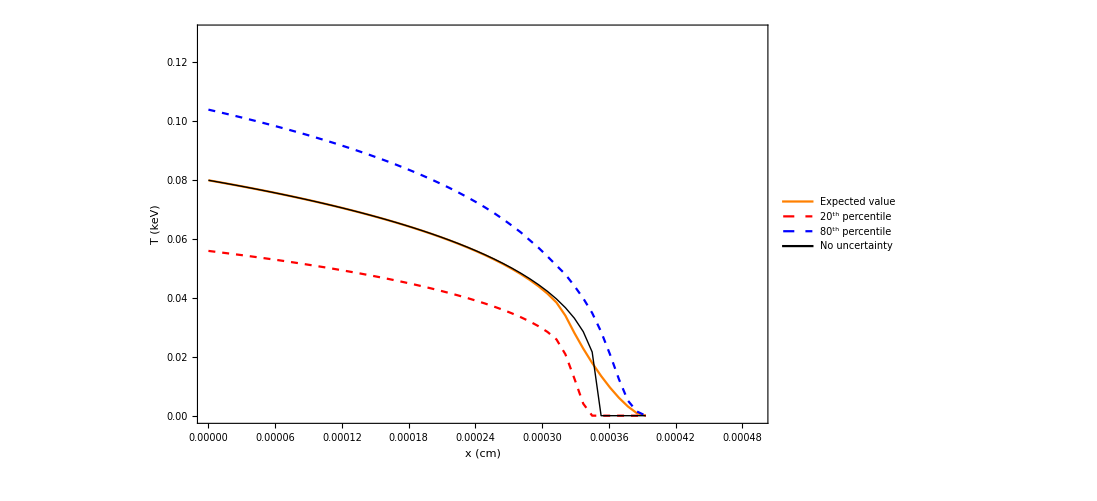

```mathematica
PlotBothPnprofile =ListPlot[{(* dataDriveDensity ,*)(*exactBoth,*) dataBoth, dataBoth20, dataBoth80 , Tnominal}, Joined -> {True, True, True, True},Frame->{True, True, False, False},FrameLabel->{Style["x (cm)", Large],Style["T (keV)", Large]},LabelStyle->Directive[Black, Bold], PlotStyle->{Orange, {Red, Dashed},{Blue, Dashed}, {Black, Thick}}, PlotRange->{{0, xlist[[Nevalpoints]] + 0.0001},{-0.0, 0.13}}, (*Epilog -> {Black, Thick, Dashed, line1},*)PlotLegends->{(*"Benchmark",*)(*"C{0,0}",*) "Expected value", "20^th percentile", "80^th percentile", "No uncertainty"}]
```

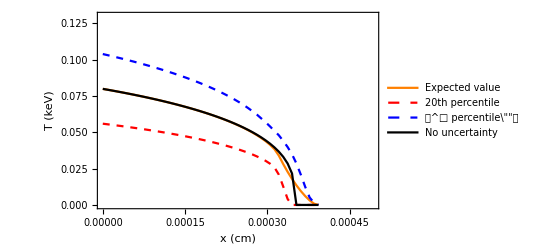

```mathematica
Export[ "BothUncertain.jpg",PlotBothPnprofile];
```

```mathematica
"80^th"
```

\left\{\$ \text{$\$$80}^{\text{th}}\right\}

```mathematica
Print[RMSE[dataDriveDensity[[1;;,2]], dataBoth[[1;;,2]]]," Sampled RMSE"];
Print[RMSE[dataDriveDensity[[1;;,2]], exactBoth[[1;;,2]]]," Exact RMSE"];
```

2.88482×10^-6 Sampled RMSE

4.06716×10^-8 Exact RMSE

# TEST

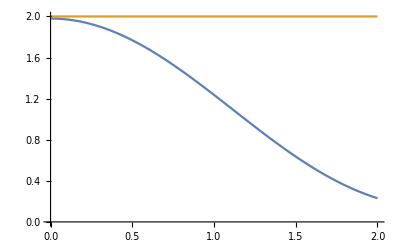

```mathematica
MMM = 10;
f[x_]:=2
Htestfunc[n_]:=NIntegrate[f[z] HBasis[n,z] Exp[-z^2]/(Sqrt[2 π] Factorial[n]), {z, -∞,∞}, WorkingPrecision->wkpc]
Htest1coeffs[M_] := Table[Htestfunc[n],{n,0,M}]
hg = Htest1coeffs[MMM];

HexpansionTest[x1_]:= Total[Table[hg[[n]]HBasis[n-1,x1],{n,1,MMM}]];

HexpansionTest[0];
Plot[{HexpansionTest[x], f[x]}, {x,0,2}]
```

```mathematica
FullSimplify[HBasis[3,x]]
```

x (-3+x^2)

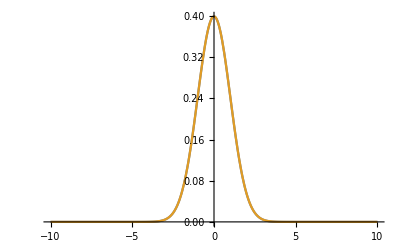

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],1/Sqrt[2 π ] Exp[(-(x)^2)/2]},{x,-10,10}, PlotRange->All]
```

```mathematica
Series[x^4,{x,1,5}]
```

1+4 (x-1)+6 (x-1)^2+4 (x-1)^3+(x-1)^4+O[x-1]^6

```mathematica
cc1 Basis[n,x] + cc2 Basis[n, x]
```

```mathematica
FullSimplify[Integrate[1/(T0 + Subscript[a, 1] x)^n,x]]
```

(T0+x a_1)^(1-n)/(a_1-n a_1)

```mathematica
FullSimplify[D[(T0+x Subscript[a, 1])^(1-n)/(Subscript[a, 1]-n Subscript[a, 1]),x]]
```

(T0+x a_1)^-n

```mathematica
1-Sqrt[2]/2
```

1-1/(√2)

```mathematica
RootReduce[1-1/(√2)]
```

1/2 (2-√2)

```mathematica
k = 8;
n = 2;
hk = 5;
```

```mathematica
AA = Table[Integrate[HermiteH[k,x]HermiteH[i,x]HermiteH[j,x]HermiteH[n,x]Exp[-x^2/2],{x,-∞,∞}],{i,0,hk},{j,0,hk}];
MatrixForm[AA]
```

(110880 √(2 π) | 0 | 7371840 √(2 π) | 0 | 448398720 √(2 π)
0 | 7593600 √(2 π) | 0 | 492629760 √(2 π) | 0
7371840 √(2 π) | 0 | 508260480 √(2 π) | 0 | 33043772160 √(2 π)
0 | 492629760 √(2 π) | 0 | 34122816000 √(2 π) | 0
448398720 √(2 π) | 0 | 33043772160 √(2 π) | 0 | 2350513267200 √(2 π))

```mathematica
Integrate[HermiteH[0,x]HermiteH[9,x]HermiteH[1,x]Exp[-x^2/2],{x,-∞,∞}]
```

60480 √(2 π)

```mathematica
AAB = Table[Integrate[Basis[i,x]Basis[j,x]Basis[k,x]Basis[n,x],{x,-1,1}],{i,0,hk},{j,0,hk}, {k,0,hk}, {n, 0, hk}];
```

```mathematica
MatrixForm[AA[[2]][[
2]]]
```

(√(2 π) | 0 | 2 √(2 π) | 0 | 0
0 | 3 √(2 π) | 0 | 6 √(2 π) | 0
2 √(2 π) | 0 | 10 √(2 π) | 0 | 24 √(2 π)
0 | 6 √(2 π) | 0 | 42 √(2 π) | 0
0 | 0 | 24 √(2 π) | 0 | 216 √(2 π))

```mathematica
AB = Table[Integrate[Basis[i,x]Basis[j,x]Basis[k,x],{x,-1,1}],{i,0,hk},{j,0,hk}, {k,0,hk}];
```

```mathematica
MatrixForm[AB[[2]]]
```

(0 | 1/(√2) | 0 | 0 | 0
1/(√2) | 0 | √(2/5) | 0 | 0
0 | √(2/5) | 0 | 3 √(3/70) | 0
0 | 0 | 3 √(3/70) | 0 | 2 √(2/21)
0 | 0 | 0 | 2 √(2/21) | 0)

```mathematica
AA = Table[Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]HBasis[n,x]Exp[-x^2/2],{x,-∞,∞}],{i,0,hk},{j,0,hk}, {k,0,hk}, {n, 0, hk}];
```

```mathematica
MatrixForm[AA]
```

((√(2 π) | 0 | 0 | 0 | 0 | 0
0 | √(2 π) | 0 | 0 | 0 | 0
0 | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 0 | 0 | 6 √(2 π) | 0 | 0
0 | 0 | 0 | 0 | 24 √(2 π) | 0
0 | 0 | 0 | 0 | 0 | 120 √(2 π)) | (0 | √(2 π) | 0 | 0 | 0 | 0
√(2 π) | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 0 | 0 | 120 √(2 π) | 0) | (0 | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
2 √(2 π) | 0 | 8 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)) | (0 | 0 | 0 | 6 √(2 π) | 0 | 0
0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 36 √(2 π) | 0 | 216 √(2 π) | 0
0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0) | (0 | 0 | 0 | 0 | 24 √(2 π) | 0
0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
24 √(2 π) | 0 | 192 √(2 π) | 0 | 1728 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)) | (0 | 0 | 0 | 0 | 0 | 120 √(2 π)
0 | 0 | 0 | 0 | 120 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)
120 √(2 π) | 0 | 1200 √(2 π) | 0 | 14400 √(2 π) | 0)
(0 | √(2 π) | 0 | 0 | 0 | 0
√(2 π) | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 0 | 0 | 120 √(2 π) | 0) | (√(2 π) | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 3 √(2 π) | 0 | 6 √(2 π) | 0 | 0
2 √(2 π) | 0 | 10 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 42 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 216 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1320 √(2 π)) | (0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
2 √(2 π) | 0 | 10 √(2 π) | 0 | 24 √(2 π) | 0
0 | 10 √(2 π) | 0 | 48 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0) | (0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 42 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 42 √(2 π) | 0 | 324 √(2 π) | 0 | 1800 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)) | (0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 216 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 216 √(2 π) | 0 | 2304 √(2 π) | 0 | 20160 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0) | (0 | 0 | 0 | 0 | 120 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1320 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0
0 | 1320 √(2 π) | 0 | 18000 √(2 π) | 0 | 216000 √(2 π))
(0 | 0 | 2 √(2 π) | 0 | 0 | 0
0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
2 √(2 π) | 0 | 8 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)) | (0 | 2 √(2 π) | 0 | 6 √(2 π) | 0 | 0
2 √(2 π) | 0 | 10 √(2 π) | 0 | 24 √(2 π) | 0
0 | 10 √(2 π) | 0 | 48 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0) | (2 √(2 π) | 0 | 8 √(2 π) | 0 | 24 √(2 π) | 0
0 | 10 √(2 π) | 0 | 48 √(2 π) | 0 | 120 √(2 π)
8 √(2 π) | 0 | 60 √(2 π) | 0 | 288 √(2 π) | 0
0 | 48 √(2 π) | 0 | 372 √(2 π) | 0 | 1920 √(2 π)
24 √(2 π) | 0 | 288 √(2 π) | 0 | 2544 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1920 √(2 π) | 0 | 19440 √(2 π)) | (0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 48 √(2 π) | 0 | 372 √(2 π) | 0 | 1920 √(2 π)
36 √(2 π) | 0 | 372 √(2 π) | 0 | 2880 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0) | (0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
24 √(2 π) | 0 | 288 √(2 π) | 0 | 2544 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
192 √(2 π) | 0 | 2544 √(2 π) | 0 | 27648 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)) | (0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1920 √(2 π) | 0 | 19440 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)
1200 √(2 π) | 0 | 19440 √(2 π) | 0 | 273600 √(2 π) | 0)
(0 | 0 | 0 | 6 √(2 π) | 0 | 0
0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 36 √(2 π) | 0 | 216 √(2 π) | 0
0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0) | (0 | 0 | 6 √(2 π) | 0 | 24 √(2 π) | 0
0 | 6 √(2 π) | 0 | 42 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 42 √(2 π) | 0 | 324 √(2 π) | 0 | 1800 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)) | (0 | 6 √(2 π) | 0 | 36 √(2 π) | 0 | 120 √(2 π)
6 √(2 π) | 0 | 48 √(2 π) | 0 | 264 √(2 π) | 0
0 | 48 √(2 π) | 0 | 372 √(2 π) | 0 | 1920 √(2 π)
36 √(2 π) | 0 | 372 √(2 π) | 0 | 2880 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0) | (6 √(2 π) | 0 | 36 √(2 π) | 0 | 216 √(2 π) | 0
0 | 42 √(2 π) | 0 | 324 √(2 π) | 0 | 1800 √(2 π)
36 √(2 π) | 0 | 372 √(2 π) | 0 | 2880 √(2 π) | 0
0 | 324 √(2 π) | 0 | 3348 √(2 π) | 0 | 25920 √(2 π)
216 √(2 π) | 0 | 2880 √(2 π) | 0 | 30672 √(2 π) | 0
0 | 1800 √(2 π) | 0 | 25920 √(2 π) | 0 | 295920 √(2 π)) | (0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
216 √(2 π) | 0 | 2880 √(2 π) | 0 | 30672 √(2 π) | 0
0 | 2304 √(2 π) | 0 | 30672 √(2 π) | 0 | 328320 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0) | (0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0
0 | 1800 √(2 π) | 0 | 25920 √(2 π) | 0 | 295920 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0
0 | 18000 √(2 π) | 0 | 295920 √(2 π) | 0 | 4104000 √(2 π))
(0 | 0 | 0 | 0 | 24 √(2 π) | 0
0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
24 √(2 π) | 0 | 192 √(2 π) | 0 | 1728 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)) | (0 | 0 | 0 | 24 √(2 π) | 0 | 120 √(2 π)
0 | 0 | 24 √(2 π) | 0 | 216 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 216 √(2 π) | 0 | 2304 √(2 π) | 0 | 20160 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0) | (0 | 0 | 24 √(2 π) | 0 | 192 √(2 π) | 0
0 | 24 √(2 π) | 0 | 264 √(2 π) | 0 | 1680 √(2 π)
24 √(2 π) | 0 | 288 √(2 π) | 0 | 2544 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
192 √(2 π) | 0 | 2544 √(2 π) | 0 | 27648 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)) | (0 | 24 √(2 π) | 0 | 216 √(2 π) | 0 | 1440 √(2 π)
24 √(2 π) | 0 | 264 √(2 π) | 0 | 2304 √(2 π) | 0
0 | 264 √(2 π) | 0 | 2880 √(2 π) | 0 | 23760 √(2 π)
216 √(2 π) | 0 | 2880 √(2 π) | 0 | 30672 √(2 π) | 0
0 | 2304 √(2 π) | 0 | 30672 √(2 π) | 0 | 328320 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0) | (24 √(2 π) | 0 | 192 √(2 π) | 0 | 1728 √(2 π) | 0
0 | 216 √(2 π) | 0 | 2304 √(2 π) | 0 | 20160 √(2 π)
192 √(2 π) | 0 | 2544 √(2 π) | 0 | 27648 √(2 π) | 0
0 | 2304 √(2 π) | 0 | 30672 √(2 π) | 0 | 328320 √(2 π)
1728 √(2 π) | 0 | 27648 √(2 π) | 0 | 368064 √(2 π) | 0
0 | 20160 √(2 π) | 0 | 328320 √(2 π) | 0 | 4466880 √(2 π)) | (0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0
0 | 20160 √(2 π) | 0 | 328320 √(2 π) | 0 | 4466880 √(2 π)
14400 √(2 π) | 0 | 273600 √(2 π) | 0 | 4466880 √(2 π) | 0)
(0 | 0 | 0 | 0 | 0 | 120 √(2 π)
0 | 0 | 0 | 0 | 120 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)
120 √(2 π) | 0 | 1200 √(2 π) | 0 | 14400 √(2 π) | 0) | (0 | 0 | 0 | 0 | 120 √(2 π) | 0
0 | 0 | 0 | 120 √(2 π) | 0 | 1320 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0
0 | 1320 √(2 π) | 0 | 18000 √(2 π) | 0 | 216000 √(2 π)) | (0 | 0 | 0 | 120 √(2 π) | 0 | 1200 √(2 π)
0 | 0 | 120 √(2 π) | 0 | 1680 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1920 √(2 π) | 0 | 19440 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)
1200 √(2 π) | 0 | 19440 √(2 π) | 0 | 273600 √(2 π) | 0) | (0 | 0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0
0 | 120 √(2 π) | 0 | 1800 √(2 π) | 0 | 18000 √(2 π)
120 √(2 π) | 0 | 1920 √(2 π) | 0 | 23760 √(2 π) | 0
0 | 1800 √(2 π) | 0 | 25920 √(2 π) | 0 | 295920 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0
0 | 18000 √(2 π) | 0 | 295920 √(2 π) | 0 | 4104000 √(2 π)) | (0 | 120 √(2 π) | 0 | 1440 √(2 π) | 0 | 14400 √(2 π)
120 √(2 π) | 0 | 1680 √(2 π) | 0 | 20160 √(2 π) | 0
0 | 1680 √(2 π) | 0 | 23760 √(2 π) | 0 | 273600 √(2 π)
1440 √(2 π) | 0 | 23760 √(2 π) | 0 | 328320 √(2 π) | 0
0 | 20160 √(2 π) | 0 | 328320 √(2 π) | 0 | 4466880 √(2 π)
14400 √(2 π) | 0 | 273600 √(2 π) | 0 | 4466880 √(2 π) | 0) | (120 √(2 π) | 0 | 1200 √(2 π) | 0 | 14400 √(2 π) | 0
0 | 1320 √(2 π) | 0 | 18000 √(2 π) | 0 | 216000 √(2 π)
1200 √(2 π) | 0 | 19440 √(2 π) | 0 | 273600 √(2 π) | 0
0 | 18000 √(2 π) | 0 | 295920 √(2 π) | 0 | 4104000 √(2 π)
14400 √(2 π) | 0 | 273600 √(2 π) | 0 | 4466880 √(2 π) | 0
0 | 216000 √(2 π) | 0 | 4104000 √(2 π) | 0 | 67003200 √(2 π)))

```mathematica
MatrixForm[AAB]
```

((1/2 | 0 | 0 | 0 | 0
0 | 1/2 | 0 | 0 | 0
0 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 1/2) | (0 | 1/2 | 0 | 0 | 0
1/2 | 0 | 1/(√5) | 0 | 0
0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | 0 | 0 | 2/(√21) | 0) | (0 | 0 | 1/2 | 0 | 0
0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
1/2 | 0 | (√5)/7 | 0 | 3/7
0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
0 | 0 | 3/7 | 0 | (10 √5)/77) | (0 | 0 | 0 | 1/2 | 0
0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
1/2 | 0 | 2/(3 √5) | 0 | 3/11
0 | 2/(√21) | 0 | 3/11 | 0) | (0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 2/(√21) | 0
0 | 0 | 3/7 | 0 | (10 √5)/77
0 | 2/(√21) | 0 | 3/11 | 0
1/2 | 0 | (10 √5)/77 | 0 | 243/1001)
(0 | 1/2 | 0 | 0 | 0
1/2 | 0 | 1/(√5) | 0 | 0
0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | 0 | 0 | 2/(√21) | 0) | (1/2 | 0 | 1/(√5) | 0 | 0
0 | 9/10 | 0 | (3 √(3/7))/5 | 0
1/(√5) | 0 | 11/14 | 0 | 6/(7 √5)
0 | (3 √(3/7))/5 | 0 | 23/30 | 0
0 | 0 | 6/(7 √5) | 0 | 117/154) | (0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
1/(√5) | 0 | 11/14 | 0 | 6/(7 √5)
0 | 11/14 | 0 | √(3/7) | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0) | (0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | (3 √(3/7))/5 | 0 | 23/30 | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | 23/30 | 0 | (6 √21)/55 | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143) | (0 | 0 | 0 | 2/(√21) | 0
0 | 0 | 6/(7 √5) | 0 | 117/154
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143
0 | 117/154 | 0 | (102 √(3/7))/143 | 0)
(0 | 0 | 1/2 | 0 | 0
0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
1/2 | 0 | (√5)/7 | 0 | 3/7
0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
0 | 0 | 3/7 | 0 | (10 √5)/77) | (0 | 1/(√5) | 0 | (3 √(3/35))/2 | 0
1/(√5) | 0 | 11/14 | 0 | 6/(7 √5)
0 | 11/14 | 0 | √(3/7) | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0) | (1/2 | 0 | (√5)/7 | 0 | 3/7
0 | 11/14 | 0 | √(3/7) | 0
(√5)/7 | 0 | 15/14 | 0 | (18 √5)/77
0 | √(3/7) | 0 | 61/66 | 0
3/7 | 0 | (18 √5)/77 | 0 | 1789/2002) | (0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | √(3/7) | 0 | 61/66 | 0
2/(3 √5) | 0 | 61/66 | 0 | 246/(143 √5)
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0) | (0 | 0 | 3/7 | 0 | (10 √5)/77
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0
3/7 | 0 | (18 √5)/77 | 0 | 1789/2002
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0
(10 √5)/77 | 0 | 1789/2002 | 0 | (270 √5)/1001)
(0 | 0 | 0 | 1/2 | 0
0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
1/2 | 0 | 2/(3 √5) | 0 | 3/11
0 | 2/(√21) | 0 | 3/11 | 0) | (0 | 0 | (3 √(3/35))/2 | 0 | 2/(√21)
0 | (3 √(3/7))/5 | 0 | 23/30 | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | 23/30 | 0 | (6 √21)/55 | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143) | (0 | (3 √(3/35))/2 | 0 | 2/(3 √5) | 0
(3 √(3/35))/2 | 0 | √(3/7) | 0 | 71/(11 √105)
0 | √(3/7) | 0 | 61/66 | 0
2/(3 √5) | 0 | 61/66 | 0 | 246/(143 √5)
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0) | (1/2 | 0 | 2/(3 √5) | 0 | 3/11
0 | 23/30 | 0 | (6 √21)/55 | 0
2/(3 √5) | 0 | 61/66 | 0 | 246/(143 √5)
0 | (6 √21)/55 | 0 | 1687/1430 | 0
3/11 | 0 | 246/(143 √5) | 0 | 291/286) | (0 | 2/(√21) | 0 | 3/11 | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0
3/11 | 0 | 246/(143 √5) | 0 | 291/286
0 | (102 √(3/7))/143 | 0 | 291/286 | 0)
(0 | 0 | 0 | 0 | 1/2
0 | 0 | 0 | 2/(√21) | 0
0 | 0 | 3/7 | 0 | (10 √5)/77
0 | 2/(√21) | 0 | 3/11 | 0
1/2 | 0 | (10 √5)/77 | 0 | 243/1001) | (0 | 0 | 0 | 2/(√21) | 0
0 | 0 | 6/(7 √5) | 0 | 117/154
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143
0 | 117/154 | 0 | (102 √(3/7))/143 | 0) | (0 | 0 | 3/7 | 0 | (10 √5)/77
0 | 6/(7 √5) | 0 | 71/(11 √105) | 0
3/7 | 0 | (18 √5)/77 | 0 | 1789/2002
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0
(10 √5)/77 | 0 | 1789/2002 | 0 | (270 √5)/1001) | (0 | 2/(√21) | 0 | 3/11 | 0
2/(√21) | 0 | 71/(11 √105) | 0 | (102 √(3/7))/143
0 | 71/(11 √105) | 0 | 246/(143 √5) | 0
3/11 | 0 | 246/(143 √5) | 0 | 291/286
0 | (102 √(3/7))/143 | 0 | 291/286 | 0) | (1/2 | 0 | (10 √5)/77 | 0 | 243/1001
0 | 117/154 | 0 | (102 √(3/7))/143 | 0
(10 √5)/77 | 0 | 1789/2002 | 0 | (270 √5)/1001
0 | (102 √(3/7))/143 | 0 | 291/286 | 0
243/1001 | 0 | (270 √5)/1001 | 0 | 42849/34034))

```mathematica
AH = Table[Integrate[HBasis[i,x]HBasis[j,x]HBasis[k,x]Exp[-x^2/2],{x,-∞,∞}],{i,0,hk},{j,0,hk}, {k,0,hk}];
```

```mathematica
MatrixForm[AH[[4]]]
```

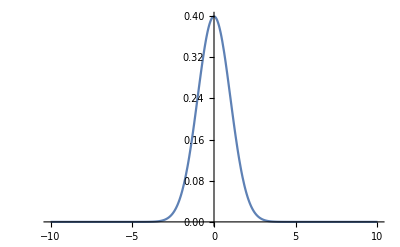

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-10,10}, PlotRange->All]
```

```mathematica
NormalDistribution[0,1]
styles=Flatten@Table[{Directive[color],Directive[Thick,color, Thick],Directive[DotDashed,color, Thick],Directive[Dotted,color, Thick]},{color,{Black,Gray}} ];
```

NormalDistribution[0,1]

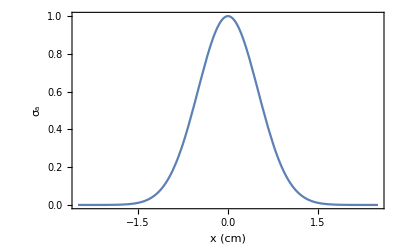

```mathematica
plot5 = Plot[{Exp[(-(x)^2)/(2*0.5^2)]},{x,-2.5,2.5}, PlotStyle->styles2, Frame->{True, True, False, False},FrameLabel->{Style["x (cm)", Large],Style["σ_a", Large]},LabelStyle->Directive[Black, Bold]]
```

```mathematica
Export["DensityPlotforPresentation.pdf",plot5]
```

DensityPlotforPresentation.pdf

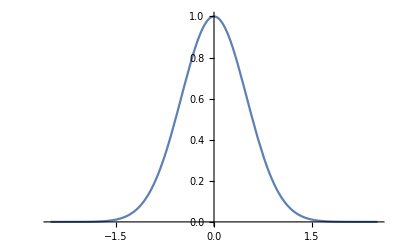

```mathematica
Plot[Exp[(-(x)^2)/(2*0.5^2)],{x,-2.5,2.5}]
```

```mathematica
Integrate[Exp[-x^2]/2,x]
```

1/4 √π Erf[x]

```mathematica
FullSimplify[Solve[μ(x-L)+t0 == v0(x-x0),x]]
```

{{x→(t0+v0 x0-L μ)/(v0-μ)}}

```mathematica
FullSimplify[μ (t0+v0 x0-L μ)/(v0-μ)+t0]
```

t0+(μ (t0+v0 x0-L μ))/(v0-μ)

```mathematica
Integrate[HeavisideTheta[x0 - Abs[s-v0(μ(x+L)+t0)]],{s,-L,x+v0(t-t0)}]
```

```mathematica
ClearAll[x]
Print[FortranForm[LegendreP[23,x]]]
```

(-2028117*x + 185910725*x**3 - 5019589575*x**5 + 62386327575*x**7 - 429772478850*x**9 + 1805044411170*x**11 - 4859734953150*x**13 + 8562390155550*x**15 - 9821565178425*x**17 + 7064634602025*x**19 - 2893136075115*x**21 + 514589420475*x**23)/524288.